# Ecological Model

Supplementary File for “Feedback between coevolution and epidemiology can help or hinder the maintenance of genetic variation in host-parasite models” 
Authors: MacPherson, Keeling, and Otto
Last Updated: November 15th, 2020

```mathematica
Clear["Global`*"]
```

## Deterministic Dynamics

```mathematica
kV=1;
```

Differential Equations

```mathematica
βSub={β[1,1]->X/(kV κ),β[1,2]->Y/(kV κ),β[2,1]->Y/(kV  κ),β[2,2]->X/(kV κ)}/.kV->1;
```

```mathematica
g1[i_,t_]:=b h[i,t](1-Sum[h[k,t],{k,1,2}]/(kV κ))-δ h[i,t]-α h[i,t]Sum[β[i,j]p[j,t],{j,1,2}]/.βSub/.kV->1
g2[j_,t_]:=p[j,t]Sum[β[i,j]h[i,t],{i,1,2}]-γ p[j,t]/.βSub/.kV->1
```

```mathematica
g1[1,t]/h[1,t]-g1[2,t]/h[2,t]//Simplify
```

-((X-Y) α (p[1,t]-p[2,t]))/κ

```mathematica
g2[1,t]/p[1,t]-g2[2,t]/p[2,t]//Simplify
```

((X-Y) (h[1,t]-h[2,t]))/κ

Equilibria and Stability

```mathematica
equs=Join[Table[g1[i,t],{i,1,2}],Table[g2[j,t],{j,1,2}]];
vars=Join[Table[h[i,t],{i,1,2}],Table[p[j,t],{j,1,2}]];
equi=Solve[equs=={0,0,0,0},vars]/.βSub//Simplify;
equiEnd=equi[[5]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{h[1,t]→(γ κ)/(X+Y),h[2,t]→(γ κ)/(X+Y),p[1,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α),p[2,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)}

Extinction. Stable if b<δ

```mathematica
equi[[11]]
```

{h[1,t]→0,h[2,t]→0,p[1,t]→0,p[2,t]→0}

Host Only.Stable if b>δ and γ>γCrit

```mathematica
equi[[{1,3,7,10}]]
```

{{h[2,t]→κ-(δ κ)/b-h[1,t],p[1,t]→0,p[2,t]→0},{h[1,t]→0,h[2,t]→κ-(δ κ)/b,p[1,t]→0,p[2,t]→0},{h[1,t]→κ-(δ κ)/b,h[2,t]→0,p[1,t]→0,p[2,t]→0},{h[1,t]→((b (-Y+γ)+Y δ) κ)/(b (X-Y)),h[2,t]→((b (X-γ)-X δ) κ)/(b (X-Y)),p[1,t]→0,p[2,t]→0}}

One host type, one pathogen type. Never stable

```mathematica
equi[[{2,4,6,8}]]
```

{{h[1,t]→0,h[2,t]→(γ κ)/X,p[1,t]→0,p[2,t]→((b (X-γ)-X δ) κ)/(X^2 α)},{h[1,t]→0,h[2,t]→(γ κ)/Y,p[1,t]→((b (Y-γ)-Y δ) κ)/(Y^2 α),p[2,t]→0},{h[1,t]→(γ κ)/Y,h[2,t]→0,p[1,t]→0,p[2,t]→((b (Y-γ)-Y δ) κ)/(Y^2 α)},{h[1,t]→(γ κ)/X,h[2,t]→0,p[1,t]→((b (X-γ)-X δ) κ)/(X^2 α),p[2,t]→0}}

One host type, one pathogen type: Stable if b>δ and γ<γCrit

```mathematica
equi[[5]]
```

{h[1,t]→(γ κ)/(X+Y),h[2,t]→(γ κ)/(X+Y),p[1,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α),p[2,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)}

## Stability

```mathematica
jMtrx={{D[g1[1,t],h[1,t]],D[g1[1,t],h[2,t]],D[g1[1,t],p[1,t]],D[g1[1,t],p[2,t]]},{D[g1[2,t],h[1,t]],D[g1[2,t],h[2,t]],D[g1[2,t],p[1,t]],D[g1[2,t],p[2,t]]},{D[g2[1,t],h[1,t]],D[g2[1,t],h[2,t]],D[g2[1,t],p[1,t]],D[g2[1,t],p[2,t]]},{D[g2[2,t],h[1,t]],D[g2[2,t],h[2,t]],D[g2[2,t],p[1,t]],D[g2[2,t],p[2,t]]}};
```

### Extinction equilibrium

```mathematica
Simplify[jMtrx/.equi[[11]]]//Eigenvalues
```

{-γ,-γ,b-δ,b-δ}

This equilibrium is stable if b<δ

### Pathogen free

```mathematica
equi[[1]]
```

{h[2,t]→κ-(δ κ)/b-h[1,t],p[1,t]→0,p[2,t]→0}

```mathematica
λs=Simplify[jMtrx/.equi[[1]]]//Eigenvalues//FullSimplify
```

{0,-b+δ,Y-γ-(Y δ)/b+((X-Y) h[1,t])/κ,X-γ-(X δ)/b+((-X+Y) h[1,t])/κ}

This equilibrium is stable if γ>((X+Y) (b-δ))/(2 b)

### Internal equilibrium (Equilibrium “neutrally stable” if γ<((X+Y) (b-δ))/(2 b) and b>δ)

#### Eigenvectors

```mathematica
testPars={b->4.03544,δ->2.06015,X->2.35543,Y->0.885944,α->0.146708,γ->0.734407,kV->1,κ->100};
```

```mathematica
Eigensystem[jMtrx/.equiEnd/.testPars][[1]]//Chop//MatrixForm
```

(-1.76772
0.+0.14878 ⅈ
0.-0.14878 ⅈ
-0.0609259)

```mathematica
Eigensystem[jMtrx/.equiEnd/.testPars][[2]]//Chop//MatrixForm
```

(0.615514 | 0.615514 | -0.348056 | -0.348056
0.-0.220567 ⅈ | 0.+0.220567 ⅈ | -0.671826 | 0.671826
0.+0.220567 ⅈ | 0.-0.220567 ⅈ | -0.671826 | 0.671826
-0.0430188 | -0.0430188 | 0.705797 | 0.705797)

#### Eigenvalues

```mathematica
CP=CharacteristicPolynomial[jMtrx/.equiEnd,λ]//Simplify//Factor
```

1/(X+Y)^4(b X γ+b Y γ-2 b γ^2-X γ δ-Y γ δ+2 b γ λ+X λ^2+Y λ^2) (b X^3 γ-b X^2 Y γ-b X Y^2 γ+b Y^3 γ-2 b X^2 γ^2+4 b X Y γ^2-2 b Y^2 γ^2-X^3 γ δ+X^2 Y γ δ+X Y^2 γ δ-Y^3 γ δ+X^3 λ^2+3 X^2 Y λ^2+3 X Y^2 λ^2+Y^3 λ^2)

Second polynomial: Determines instability vs. neutral stability

```mathematica
Solve[CP[[3]]==0,λ]//Simplify
```

{{λ→-(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(√((X+Y)^3))},{λ→(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(√((X+Y)^3))}}

```mathematica
Reduce[{b (X+Y-2 γ)-(X+Y) δ>0,0<Y<X,0<δ<b,0<γ}]//FullSimplify
```

0<Y<X&&δ>0&&b>δ&&0<γ<((X+Y) (b-δ))/(2 b)

The equilibrium will be neutrally stable if γ<((X+Y) (b-δ))/(2 b)

First polynomial: Determines cycling behavior of

Routh-Hurwitz conditions for stability for these two eigenvalues

```mathematica
Solve[CP[[2]]==0,λ]//Simplify
```

{{λ→-(b γ+√(γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/(X+Y)},{λ→(-b γ+√(γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/(X+Y)}}

```mathematica
Collect[CP[[2]],λ]
```

b X γ+b Y γ-2 b γ^2-X γ δ-Y γ δ+2 b γ λ+(X+Y) λ^2

```mathematica
aList=CoefficientList[CP[[2]]/Coefficient[CP[[2]],λ^2],λ]//Simplify
```

{(γ (b (X+Y-2 γ)-(X+Y) δ))/(X+Y),(2 b γ)/(X+Y),1}

```mathematica
Reduce[{aList[[1]]>0,aList[[2]]>0,0<Y<X,0<δ<b,0<γ}]//Simplify
```

Y>0&&X>Y&&δ>0&&b>δ&&0<γ<((X+Y) (b-δ))/(2 b)

Determining stability of population size

```mathematica
arg=γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ);
```

```mathematica
Reduce[{arg>0,0<Y<X,0<δ<b,0<γ}]//Simplify
```

Y>0&&X>Y&&b>0&&0<δ<b&&γ>((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))

The population size will not cycle if γ>((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))

```mathematica
γ<((X+Y) (b-δ))/(2 b)/.simPars[fileV,2,3]
```

True

```mathematica
γ>((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))/.simPars[fileV,2,3]
```

True

```mathematica
(((X+Y)^2 (b-δ))/(b (b+2 (X+Y))))/(((X+Y) (b-δ))/(2 b))//Simplify
```

(2 (X+Y))/(b+2 (X+Y))

```mathematica
jMtrx/.equiEnd/.simPars[fileV,2,3]//Eigenvalues//Chop
```

{-721.299,0.+0.030507 ⅈ,0.-0.030507 ⅈ,-0.000283104}

Change of Variables

```mathematica
Clear[nH,nP,pH,pP]
```

```mathematica
varSub={h[2,t]->nH[t]-pH[t]nH[t],p[2,t]->nP[t]-pP[t]nP[t],h[1,t]->pH[t]nH[t],p[1,t]->pP[t]nP[t]};
```

```mathematica
fH[t_]:=g1[1,t]+g1[2,t]/.varSub//FullSimplify
fP[t_]:=g2[1,t]+g2[2,t]/.varSub//FullSimplify
fH2[t_]:=g1[1,t]/(h[1,t]+h[2,t])-(h[1,t](g1[1,t]+g1[2,t]))/(h[1,t]+h[2,t])^2 /.varSub//FullSimplify
fP2[t_]:=g2[1,t]/(p[1,t]+p[2,t])-(p[1,t](g2[1,t]+g2[2,t]))/(p[1,t]+p[2,t])^2/.varSub//FullSimplify
```

```mathematica
equsNew={fH[t],fH2[t],fP[t],fP2[t]};
```

```mathematica
Clear[equs]
```

```mathematica
equiNew=Solve[equsNew=={0,0,0,0},{nH[t],pH[t],nP[t],pP[t]}]//Simplify;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
equiNew[[19]]//FullSimplify
```

{nH[t]→(2 γ κ)/(X+Y),pH[t]→1/2,nP[t]→(2 (b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α),pP[t]→1/2}

```mathematica
Clear[jMtrx2]
```

```mathematica
jMtrxNew=
{{D[fH[t],nH[t]],D[fH[t],pH[t]],D[fH[t],nP[t]],D[fH[t],pP[t]]},{D[fH2[t],nH[t]],D[fH2[t],pH[t]],D[fH2[t],nP[t]],D[fH2[t],pP[t]]},{D[fP[t],nH[t]],D[fP[t],pH[t]],D[fP[t],nP[t]],D[fP[t],pP[t]]},{D[fP2[t],nH[t]],D[fP2[t],pH[t]],D[fP2[t],nP[t]],D[fP2[t],pP[t]]}}/.equiNew[[19]]//Simplify
```

{{-(2 b γ)/(X+Y),0,-α γ,0},{0,0,0,-((X-Y) (b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^2},{(b (X+Y-2 γ)-(X+Y) δ)/((X+Y) α),0,0,0},{0,((X-Y) γ)/(X+Y),0,0}}

```mathematica
jMtrxNew//Eigenvalues//FullSimplify
```

{-(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^(3/2),(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^(3/2),-(b (X+Y) α γ+√((X+Y)^2 α^2 γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/((X+Y)^2 α),(-b (X+Y) α γ+√((X+Y)^2 α^2 γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/((X+Y)^2 α)}

```mathematica
testPars={b->4.03544,δ->2.06015,X->2.35543,Y->0.885944,α->0.146708,γ->0.734407,kV->1,κ->100};
```

```mathematica
Eigensystem[jMtrxNew][[1]]//Simplify//MatrixForm
```

(-(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^(3/2)
(ⅈ (X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^(3/2)
-(b (X+Y) α γ+√(-(X+Y)^2 α^2 γ (b (X+Y) (X+Y-2 γ)-b^2 γ-(X+Y)^2 δ)))/((X+Y)^2 α)
(-b (X+Y) α γ+√(-(X+Y)^2 α^2 γ (b (X+Y) (X+Y-2 γ)-b^2 γ-(X+Y)^2 δ)))/((X+Y)^2 α))

```mathematica
Eigensystem[jMtrxNew][[2]]//Simplify//MatrixForm
```

(0 | -(ⅈ √(b (X+Y-2 γ)-(X+Y) δ))/(√(X+Y) √γ) | 0 | 1
0 | (ⅈ √(b (X+Y-2 γ)-(X+Y) δ))/(√(X+Y) √γ) | 0 | 1
-(b (X+Y) α γ+√(-(X+Y)^2 α^2 γ (b (X+Y) (X+Y-2 γ)-b^2 γ-(X+Y)^2 δ)))/((X+Y) (b (X+Y-2 γ)-(X+Y) δ)) | 0 | 1 | 0
(-b (X+Y) α γ+√(-(X+Y)^2 α^2 γ (b (X+Y) (X+Y-2 γ)-b^2 γ-(X+Y)^2 δ)))/((X+Y) (b (X+Y-2 γ)-(X+Y) δ)) | 0 | 1 | 0)

```mathematica
(*Condition for a complex leading "Allele frequency" eigenvalue*)
Reduce[{b (X+Y-2 γ)-(X+Y) δ>0,0<δ<b,0<Y<X,0<α}]//Simplify
```

α>0&&δ>0&&b>δ&&Y>0&&X>Y&&γ<((X+Y) (b-δ))/(2 b)

```mathematica
(*Condition for a complex "population size" eigenvalue*)
Reduce[{-(X+Y)^2 α^2 γ (b (X+Y) (X+Y-2 γ)-b^2 γ-(X+Y)^2 δ)<0,0<δ<b,0<Y<X,0<α}]//Simplify
```

Y>0&&X>Y&&b>0&&0<δ<b&&0<γ<((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))&&α>0

If the “population size” eigenvalue is complex (γ<((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))) than the Real part of it is given by

```mathematica
-(b (X+Y) α γ)/((X+Y)^2 α)//FullSimplify
```

-(b γ)/(X+Y)

If the “population size” eigenvalue is real (γ>((X+Y)^2 (b-δ))/(b (b+2 (X+Y)))) the the real part of the eigenvalue is given by:

```mathematica
Simplify[-(b (X+Y) α γ+√((X+Y)^2 α^2 γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/((X+Y)^2 α),Assumptions->{0<Y<X,0<α}]
```

-(b γ+√(γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/(X+Y)

Numerical Integration

### Functions

```mathematica
Nequs[pars_]:=Join[Table[D[h[i,t],t]==g1[i,t],{i,1,2}],Table[D[p[j,t],t]==g2[j,t],{j,1,2}]]/.pars;
Ninits[pars_]:=
(*Initial Conditions for estimating r*)(*Join[Table[h[i,0]==h[i,t]*If[i==1,0.8,1.2],{i,1,2}],Table[p[j,0]==p[j,t]*If[j==1,0.8,1.2],{j,1,2}]]/.equiEnd/.pars;*)
(*Initial Conditions for numerical dynamis plots*)
Join[Table[h[i,0]==h[i,t]*If[i==1,0.2,1.8],{i,1,2}],Table[p[j,0]==p[j,t]*If[j==1,0.2,1.8],{j,1,2}]]/.equiEnd/.pars;
NinitsSub[pars_]:=Join[Table[h[i,0]->h[i,t]*If[i==1,0.2,1.8],{i,1,2}],Table[p[j,0]->p[j,t]*If[j==1,0.2,1.8],{j,1,2}]]/.equiEnd/.pars;
Nvars=Join[Table[h[i,t],{i,1,2}],Table[p[j,t],{j,1,2}]];
```

```mathematica
Ninits[simPars[fileV,1,3]]
```

ReplaceAll::reps: {equiEnd} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {simPars[fileV,1,3]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{h[1,0]==0.2 h[1,t],h[2,0]==1.8 h[2,t],p[1,0]==0.2 p[1,t],p[2,0]==1.8 p[2,t]}/.equiEnd/.simPars[fileV,1,3]

```mathematica
Clear[nSol]
nSol[pars_,tMax_]:=nSol[pars,tMax]=NDSolve[Join[Nequs[pars],Ninits[pars]],Nvars,{t,0,tMax}]//Flatten
```

```mathematica
Nhsol[pars_,tMax_,i_,τ_]:=h[i,t]/.nSol[pars,tMax]/.{t->τ}
Npsol[pars_,tMax_,j_,τ_]:=p[j,t]/.nSol[pars,tMax]/.{t->τ}
NhTsol[pars_,tMax_,τ_]:=Sum[h[i,t],{i,1,2}]/.nSol[pars,tMax]/.{t->τ}
NpTsol[pars_,tMax_,τ_]:=Sum[p[i,t],{i,1,2}]/.nSol[pars,tMax]/.{t->τ}
NpHsol[pars_,tMax_,τ_]:=h[1,t]/Sum[h[i,t],{i,1,2}]/.nSol[pars,tMax]/.{t->τ}
NpPsol[pars_,tMax_,τ_]:=p[1,t]/Sum[p[i,t],{i,1,2}]/.nSol[pars,tMax]/.{t->τ}
```

Condition for neutral stability of AF and real “population size” eigenvalues

```mathematica
Clear[nlFitPars]
nlFitPars[file_,run_,rep_]:=nlFitPars[file,run,rep]=Block[{dataTemp,testPars,period,nlFit},
period=((X-Y) √γ √(b (X+Y-2 γ)-(X+Y) δ))/(X+Y)^(3/2);
testPars=simPars[file,run,rep];
dataTemp=Table[{x,NpHsol[testPars,1000,x]-0.5},{x,0,1000}];
nlFit=NonlinearModelFit[dataTemp,{a Exp[r t]Sin[(period/.testPars) t+t0],r<0},{a,r,t0},t];
(*Show[ListLinePlot[dataTemp,PlotStyle->Black],Plot[nlFit[t],{t,0,1000}]]*)
nlFit["BestFitParameters"]]
```

### Plots

These plots use the parameters from the simulations.  Run the Individual-Based Simulations>Importing values>Parameters and Data section to obtain these parameters.

```mathematica
simPars[fileV,1,6]
```

{b→0.60136,δ→0.180789,X→0.732869,Y→0.169459,α→0.839719,γ→0.193577,κ→4144.58}

```mathematica
simPars[fileV,2,6]
```

{b→722.26,δ→0.515693,X→0.490989,Y→0.428888,α→0.968536,γ→0.459327,κ→1780.65}

```mathematica
DetAFPlot[file_,run_,rep_,color_,tMax_]:=Show[ListLinePlot[Table[{NpHsol[simPars[file,run,rep],tMax,τ],NpPsol[simPars[file,run,rep],tMax,τ]},{τ,0,tMax}],PlotStyle->color]/.Line[x_]:>{Arrowheads[Table[.05,{r,{2}}]],Arrow[x]},ListPlot[{{h[1,0]/(h[1,0]+h[2,0]),p[1,0]/(p[1,0]+p[2,0])}/.NinitsSub[simPars[file,run,rep]]},PlotStyle->Red,PlotMarkers->{●,14}],PlotRange->{{0,1},{0,1}},AspectRatio->1,ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

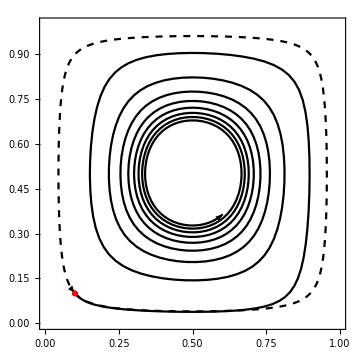

```mathematica
Show[DetAFPlot[fileV,1,6,Black,500],DetAFPlot[fileV,2,6,Directive[Black,Dashed],286]]
Export[NotebookDirectory[]<>"Plots/Eco_Det_AF2.pdf",%,ImageResolution->300];
```

```mathematica
DetHetPlot[file_,run_,rep_,color_]:=Show[ListLinePlot[Table[{τ,2NpHsol[simPars[file,run,rep],500,τ](1-NpHsol[simPars[file,run,rep],500,τ])},{τ,0,500}],PlotStyle->color,PlotRange->{0,0.5}],ListPlot[{{0,2 h[1,0]/(h[1,0]+h[2,0])(1-h[1,0]/(h[1,0]+h[2,0]))}/.NinitsSub[simPars[file,run,rep]]},PlotStyle->Red,PlotMarkers->{●,14}],ImageSize->Medium,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]
```

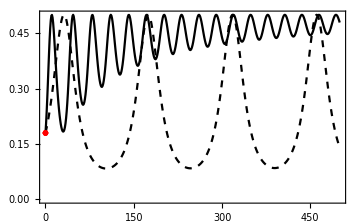

```mathematica
Show[DetHetPlot[fileV,1,6,Black],DetHetPlot[fileV,2,6,Directive[Black,Dashed]]]
Export[NotebookDirectory[]<>"Plots/Eco_Det_Het.pdf",%,ImageResolution->300];
```

Neutral Expectation

Given a stochastic sample path (i.e. the value of h[1,t], h[2,t], p[1,t], p[2,t]) for all time t we derive the neutral expectation for the heterozygosity at a neutral (unlinked) locus.  We do so by considering the effect birth and death event on the heterozygosity. Although there are multiple ways of obtaining this solution we do so by considering the effect of each event on the allele frequency at the neutral locus and the resulting change in heterozygosity H=2p(1-p)

The resulting differential equation for the change in heterozygosity given birth and death rates λ and μ is given by:

d/dt H[t]=-H(λ/(1+n)^2+μ/(n-1)^2)
where n=h[1,t]+h[2,t]

## Effect of individual birth and death events on heterozygosity

### Birth event

```mathematica
Expand[(p (2p2 (1-p2)/.p2->(n p+1)/(n+1)))+((1-p)(2p2 (1-p2)/.p2->(n p)/(n+1)))-2p(1-p)]/.{p^2->(-H+2p)/2}//FullSimplify
```

-H/(1+n)^2

### Death event

```mathematica
Expand[(p (2p2 (1-p2)/.p2->(n p-1)/(n-1)))+((1-p)(2p2 (1-p2)/.p2->(n p)/(n-1)))-2p(1-p)]/.{p^2->(-H+2p)/2}//FullSimplify
```

-H/(-1+n)^2

## Simulations

We can check the analytical approximation for the mean dynamics by comparing them against a simple birth-death simulation.

```mathematica
λ[n1_,n2_]:=Max[0,b (1-(n1+n2)/(kV κ))];
μ[n1_,n2_]:=δ;
```

```mathematica
TotalRate[n1_,n2_,pars_]:=λ[n1,n2]n1+μ[n1,n2]n1+λ[n1,n2]n2+μ[n1,n2]n2/.pars
samp[n1_,n2_,pars_]:=Block[{out,Δt},
Δt=RandomVariate[ExponentialDistribution[TotalRate[n1,n2,pars]]];
RandomChoice[{λ[n1,n2]n1/.pars,μ[n1,n2]n1/.pars,λ[n1,n2]n2/.pars,μ[n1,n2]n2/.pars}-> {{Δt,1,0},{Δt,-1,0},{Δt,0,1},{Δt,0,-1}}]]
```

```mathematica
sim[n0_,nRep_,pars_]:=Module[{out,OUT,e,r},OUT={};
For[r=1,r≤nRep,r++,
out={{0,Round[n0/2],Round[n0/2]}};
While[out[[-1,1]]<tMax/.pars,
If[Total[out[[-1,{2,3}]]]==0,AppendTo[out,{tMax/.pars,0,0}],
AppendTo[out,out[[-1]]+samp[out[[-1,2]],out[[-1,3]],pars]]
]
];
AppendTo[OUT,out]
];
OUT
]
```

```mathematica
Pars={b->0.5,δ->0.2,κ->1000,tMax->2};
```

```mathematica
ExampleSims=sim[400,1000,Pars];
NDyn=Map[Map[{#[[1]],#[[2]]+#[[3]]}&,#]&,ExampleSims];
AFDyn=Map[Map[{#[[1]],(#[[2]])/(#[[2]]+#[[3]])}&,#]&,ExampleSims]//N;
(*MeanGV=Mean[AFDyn(1-AFDyn)]//N;*)
```

```mathematica
Clear[AFDynTab]
AFDynTab[npts_,AFDyn_,pars_]:=AFDynTab[npts,AFDyn,pars]=Block[{f,e,r,out,OUT},OUT={};
For[r=1,r≤Length[AFDyn],r++,
out={{0,0.5}};
f=Interpolation[AFDyn[[r]],InterpolationOrder->0];
For[e=1,e≤npts,e++,
AppendTo[out,{e (tMax/.pars)/npts,f[e (tMax/.pars)/npts]}];
];
AppendTo[OUT,out];
];
OUT]
```

```mathematica
GraphicsRow[{ListLinePlot[NDyn,PlotStyle->Directive[Gray,Opacity[0.2]]],ListLinePlot[AFDynTab[40,AFDyn,Pars],PlotRange->{0,1},PlotStyle->Directive[Red,Opacity[0.05]]]}]
```

-Graphics-

```mathematica
GV[npts_,AFDyn_,pars_]:=Map[Map[{#[[1]],2#[[2]](1-#[[2]])}&,#]&, AFDynTab[npts,AFDyn,pars]]
```

```mathematica
Clear[GVExp];(*Clear[finalnum];*)
GVExp[npts_,NDyn_,pars_]:=GVExp[npts,NDyn,pars]=Block[{r,n1,n2,nSol,Hsol,out},out={};
For[r=1,r≤Min[500,Length[NDyn]](*Approximation for speed purposes*),r++,
n1=Interpolation[ExampleSims[[r,;;,{1,2}]],InterpolationOrder->0];
n2=Interpolation[ExampleSims[[r,;;,{1,3}]],InterpolationOrder->0];
nSol=Flatten[NDSolve[{D[H[t],t]==-H[t](n1[t]+n2[t])(λ[n1[t],n2[t]]/(n1[t]+n2[t]+1)^2+μ[n1[t],n2[t]]/(n1[t]+n2[t]-1)^2)/.Pars,H[0]==1/2//N},H[t],{t,0,tMax/.Pars}]];
Clear[Hsol];
Hsol[τ_]:=Hsol[τ]=H[t]/.nSol/.{t->τ};
(*finalnum[r]=n1[tMax/.pars]+n2[tMax/.pars];
Hsolfinal[r]=((-1+n) n (2+births^2+3 n+n^2+births (3+2 n)))/(2 (1+n) (2+n) (-1+births+n) (births+n))/.births->finalnum[r]-n/.n->400;*)
AppendTo[out,Table[{τ,Hsol[τ]},{τ,0,tMax/.pars, (tMax/.pars)/npts}]];
];
out
]
```

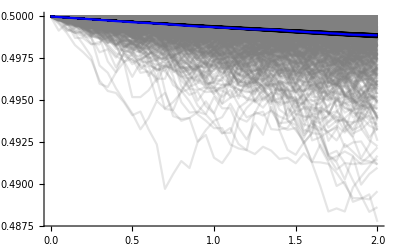

```mathematica
Show[ListLinePlot[GV[40,AFDyn,Pars],PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.2]]],ListLinePlot[GVExp[40,NDyn,Pars],PlotStyle->Directive[Black,Thick]],ListLinePlot[Mean[GV[40,AFDyn,Pars]],PlotStyle->Blue](*,PlotRange->{All,{0.498,0.5}}*)]
```

## Ensemble Moment Dynamics

Substitutions

### Moment Substitutions

```mathematica
first=Join[Table[δH[i]->μδH[i],{i,1,2}],Table[δP[i]->μδP[i],{i,1,2}]];
```

```mathematica
second=Block[{out},out={};
Table[AppendTo[out,Solve[CδHH[i1,i2]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])]/.δH[i1]δH[i2]->X,X][[1]]/.first/.X-> δH[i1]δH[i2]],{i1,1,2},{i2,i1,2}];
Table[AppendTo[out,Solve[CδHP[i1,i2]==Expand[(δH[i1]-μδH[i1])(δP[i2]-μδP[i2])]/.δH[i1]δP[i2]->X,X][[1]]/.first/.X->δH[i1]δP[i2]],{i1,1,2},{i2,1,2}];
Table[AppendTo[out,Solve[CδPP[i1,i2]==Expand[(δP[i1]-μδP[i1])(δP[i2]-μδP[i2])]/.δP[i1]δP[i2]->X,X][[1]]/.first/.X->δP[i1]δP[i2]],{i1,1,2},{i2,i1,2}];
Flatten[out]
];
```

```mathematica
third=Block[{out},out={};
Table[AppendTo[out,Solve[CδHHH[i1,i2,i3]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])(δH[i3]-μδH[i3])]/.δH[i1]δH[i2]δH[i3]->X,X][[1]]/.second/.first/.X->δH[i1]δH[i2]δH[i3]],{i1,1,2},{i2,i1,2},{i3,i2,2}];
Table[AppendTo[out,Solve[CδHHP[i1,i2,i3]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])(δP[i3]-μδP[i3])]/.δH[i1]δH[i2]δP[i3]->X,X][[1]]/.second/.first/.X->δH[i1]δH[i2]δP[i3]],{i1,1,2},{i2,i1,2},{i3,1,2}];
Table[AppendTo[out,Solve[CδHPP[i1,i2,i3]==Expand[(δH[i1]-μδH[i1])(δP[i2]-μδP[i2])(δP[i3]-μδP[i3])]/.δH[i1]δP[i2]δP[i3]->X,X][[1]]/.second/.first/.X->δH[i1]δP[i2]δP[i3]],{i1,1,2},{i2,1,2},{i3,i2,2}];
Table[AppendTo[out,Solve[CδPPP[i1,i2,i3]==Expand[(δP[i1]-μδP[i1])(δP[i2]-μδP[i2])(δP[i3]-μδP[i3])]/.δP[i1]δP[i2]δP[i3]->X,X][[1]]/.second/.first/.X->δP[i1]δP[i2]δP[i3]],{i1,1,2},{i2,i1,2},{i3,i2,2}];
Flatten[out]
];
```

```mathematica
fourth=Block[{out},out={};
Table[AppendTo[out,Solve[CδHHHH[i1,i2,i3,i4]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])(δH[i3]-μδH[i3])(δH[i4]-μδH[i4])]/.δH[i1]δH[i2]δH[i3]δH[i4]->X,X][[1]]/.second/.first/.X->δH[i1]δH[i2]δH[i3]δH[i4]],{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,i3,2}];
Table[AppendTo[out,Solve[CδHHHP[i1,i2,i3,i4]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])(δH[i3]-μδH[i3])(δP[i4]-μδP[i4])]/.δH[i1]δH[i2]δH[i3]δP[i4]->X,X][[1]]/.second/.first/.X->δH[i1]δH[i2]δH[i3]δP[i4]],{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,1,2}];
Table[AppendTo[out,Solve[CδHHPP[i1,i2,i3,i4]==Expand[(δH[i1]-μδH[i1])(δH[i2]-μδH[i2])(δP[i3]-μδP[i3])(δP[i4]-μδP[i4])]/.δH[i1]δH[i2]δP[i3]δP[i4]->X,X][[1]]/.second/.first/.X->δH[i1]δH[i2]δP[i3]δP[i4]],{i1,1,2},{i2,i1,2},{i3,1,2},{i4,i3,2}];
Table[AppendTo[out,Solve[CδHPPP[i1,i2,i3,i4]==Expand[(δH[i1]-μδH[i1])(δP[i2]-μδP[i2])(δP[i3]-μδP[i3])(δP[i4]-μδP[i4])]/.δH[i1]δP[i2]δP[i3]δP[i4]->X,X][[1]]/.second/.first/.X->δH[i1]δP[i2]δP[i3]δP[i4]],{i1,1,2},{i2,1,2},{i3,i2,2},{i4,i3,2}];
Table[AppendTo[out,Solve[CδPPPP[i1,i2,i3,i4]==Expand[(δP[i1]-μδP[i1])(δP[i2]-μδP[i2])(δP[i3]-μδP[i3])(δP[i4]-μδP[i4])]/.δP[i1]δP[i2]δP[i3]δP[i4]->X,X][[1]]/.second/.first/.X->δP[i1]δP[i2]δP[i3]δP[i4]],{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,i3,2}];
Flatten[out]
];
```

### Simplification

Let δH[i]=H[i]-OverHat[H[i]] and δP[i]=P-OverHat[P[i]].  We will assume that the deviations from equilibrium, δH and δP, are small.

Note that the covariance between the deviations from equilibrium are equal to the the covariance in the original variables.

```mathematica
eSub=Join[Table[H[i]->h[i,t]+ϵ δH[i],{i,1,2}],Table[P[i]->p[i,t]+ϵ δP[i],{i,1,2}]]/.equiEnd//Simplify
```

{H[1]→(γ κ)/(X+Y)+ϵ δH[1],H[2]→(γ κ)/(X+Y)+ϵ δH[2],P[1]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)+ϵ δP[1],P[2]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)+ϵ δP[2]}

```mathematica
μeSubRev=Flatten[Join[Table[μδH[i]->μH[i,t]-h[i,t],{i,1,2}],Table[μδP[i]->μP[i,t]-p[i,t],{i,1,2}],Table[CδHH[i1,i2]-> CHH[i1,i2,t],{i1,1,2},{i2,i1,2}],Table[CδHP[i1,i2]-> CHP[i1,i2,t],{i1,1,2},{i2,1,2}],Table[CδPP[i1,i2]-> CPP[i1,i2,t],{i1,1,2},{i2,i1,2}],Table[CδHHH[i1,i2,i3]-> CHHH[i1,i2,i3,t],{i1,1,2},{i2,i1,2},{i3,i2,2}],Table[CδHHP[i1,i2,i3]-> CHHP[i1,i2,i3,t],{i1,1,2},{i2,i1,2},{i3,1,2}],Table[CδHPP[i1,i2,i3]-> CHPP[i1,i2,i3,t],{i1,1,2},{i2,1,2},{i3,i2,2}],Table[CδPPP[i1,i2,i3]-> CPPP[i1,i2,i3,t],{i1,1,2},{i2,i1,2},{i3,i2,2}]]]/.equiEnd;
```

### Moment Closure

```mathematica
assump3=Flatten[Join[Table[CδHHHH[i1,i2,i3,i4]->0,{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,i3,2}],Table[CδHHHP[i1,i2,i3,i4]->0,{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,1,2}],Table[CδHHPP[i1,i2,i3,i4]->0,{i1,1,2},{i2,i1,2},{i3,1,2},{i4,i3,2}],Table[CδHPPP[i1,i2,i3,i4]->0,{i1,1,2},{i2,1,2},{i3,i2,2},{i4,i3,2}],Table[CδPPPP[i1,i2,i3,i4]->0,{i1,1,2},{i2,i1,2},{i3,i2,2},{i4,i3,2}]]];
```

```mathematica
assump2=Flatten[Join[Table[CδHHH[i1,i2,i3]->0,{i1,1,2},{i2,i1,2},{i3,i2,2}],Table[CδHHP[i1,i2,i3]->0,{i1,1,2},{i2,i1,2},{i3,1,2}],Table[CδHPP[i1,i2,i3]->0,{i1,1,2},{i2,1,2},{i3,i2,2}],Table[CδPPP[i1,i2,i3]->0,{i1,1,2},{i2,i1,2},{i3,i2,2}],assump3]];
```

```mathematica
assump1=Join[Table[CδHH[i1,i2]->0,{i1,1,2},{i2,i1,2}],Table[CδHP[i1,i2]->0,{i1,1,2},{i2,1,2}],Table[CδPP[i1,i2]->0,{i1,1,2},{i2,i1,2}],assump2]//Flatten;
```

Rates f[x] and change in x

```mathematica
fEco:=Join[(*Host birth*)Table[b H[i](1-Sum[H[k],{k,1,2}]/(kV κ)),{i,1,2}],
(*Nautral Host death*)Table[δ H[i],{i,1,2}],
(*Infection w/out death*)Table[(1-α)β[i,j]H[i]P[j],{i,1,2},{j,1,2}],
(*Infection w/ death*)Table[α β[i,j]H[i]P[j],{i,1,2},{j,1,2}],
(*Free-living pathogen death*)
Table[γ P[j],{j,1,2}]
]/.βSub//Flatten
```

```mathematica
ΔH[h_]:=Join[(*Host birth*)Table[If[i==h,1,0],{i,1,2}],
(*Nautral Host death*)Table[If[i==h,-1,0],{i,1,2}],
(*Infection w/out death*)Table[0,{i,1,2},{j,1,2}],
(*Infection w/ death*)Table[If[i==h,-1,0],{i,1,2},{j,1,2}],
(*Free-living pathogen death*)Table[0,{j,1,2}]
]//Flatten
```

```mathematica
ΔP[p_]:=Join[(*Host birth*)Table[0,{i,1,2}],
(*Nautral Host death*)Table[0,{i,1,2}],
(*Infection w/out death*)Table[If[j==p,1,0],{i,1,2},{j,1,2}],
(*Infection w/ death*)Table[If[j==p,1,0],{i,1,2},{j,1,2}],
(*Free-living pathogen death*)Table[If[j==p,-1,0],{j,1,2}]
]//Flatten
```

Differential Equations

## Means

```mathematica
Clear[dμHdt]
dμHdt[i_,t_]:=dμHdt[i,t]=Expand[Normal[Series[fEco.ΔH[i]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP}]/.third/.second/.first/.{ϵ->1}/.μeSubRev/.{τ->t}//Simplify
```

```mathematica
Clear[dμPdt]
dμPdt[i_,t_]:=dμPdt[i,t]=Expand[Normal[Series[fEco.ΔP[i]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP}]/.third/.second/.first/.{ϵ->1}/.μeSubRev/.{τ->t}//Simplify
```

## Variances

```mathematica
Clear[dHHdt]
dHHdt[i1_,i2_,t_]:=dHHdt[i1,i2,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(H[i1]+ΔH[i1])(H[i2]+ΔH[i2])-H[i1]H[i2]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
dHHdt[1,2,t]//Simplify
```

-1/κ(2 b CHHH[1,1,2,t]+2 b CHHH[1,2,2,t]+X α CHHP[1,2,1,t]+Y α CHHP[1,2,1,t]+X α CHHP[1,2,2,t]+Y α CHHP[1,2,2,t]+2 b CHH[2,2,t] μH[1,t]+X α CHP[2,1,t] μH[1,t]+Y α CHP[2,1,t] μH[1,t]+X α CHP[2,2,t] μH[1,t]+Y α CHP[2,2,t] μH[1,t]+2 b CHH[1,1,t] μH[2,t]+X α CHP[1,1,t] μH[2,t]+Y α CHP[1,1,t] μH[2,t]+X α CHP[1,2,t] μH[2,t]+Y α CHP[1,2,t] μH[2,t]-2 b κ μH[1,t] μH[2,t]+2 δ κ μH[1,t] μH[2,t]+2 b μH[1,t]^2 μH[2,t]+2 b μH[1,t] μH[2,t]^2+X α μH[1,t] μH[2,t] μP[1,t]+Y α μH[1,t] μH[2,t] μP[1,t]+X α μH[1,t] μH[2,t] μP[2,t]+Y α μH[1,t] μH[2,t] μP[2,t]+CHH[1,2,t] (-2 b κ+2 δ κ+4 b μH[1,t]+4 b μH[2,t]+X α μP[1,t]+Y α μP[1,t]+X α μP[2,t]+Y α μP[2,t]))

```mathematica
Clear[dHPdt]
dHPdt[i1_,i2_,t_]:=dHPdt[i1,i2,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(H[i1]+ΔH[i1])(P[i2]+ΔP[i2])-H[i1]P[i2]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPdt]
dPPdt[i1_,i2_,t_]:=dPPdt[i1,i2,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(P[i1]+ΔP[i1])(P[i2]+ΔP[i2])-P[i1]P[i2]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHdt,dCHPdt,dCPPdt]
dCHHdt[i1_,i2_,t_]:=dCHHdt[i1,i2,t]=dHHdt[i1,i2,t]-μH[i1,t]dμHdt[i2,t]-μH[i2,t]dμHdt[i1,t]//Simplify
dCHPdt[i1_,i2_,t_]:=dCHPdt[i1,i2,t]=dHPdt[i1,i2,t]-μH[i1,t]dμPdt[i2,t]-μP[i2,t]dμHdt[i1,t]//Simplify
dCPPdt[i1_,i2_,t_]:=dCPPdt[i1,i2,t]=dPPdt[i1,i2,t]-μP[i1,t]dμPdt[i2,t]-μP[i2,t]dμPdt[i1,t]//Simplify
```

## Skews

```mathematica
Clear[dHHHdt]
dHHHdt[i1_,i2_,i3_,t_]:=dHHHdt[i1,i2,i3,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(H[i1]+ΔH[i1])(H[i2]+ΔH[i2])(H[i3]+ΔH[i3])-H[i1]H[i2]H[i3]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHHPdt]
dHHPdt[i1_,i2_,i3_,t_]:=dHHPdt[i1,i2,i3,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(H[i1]+ΔH[i1])(H[i2]+ΔH[i2])(P[i3]+ΔP[i3])-H[i1]H[i2]P[i3]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHPPdt]
dHPPdt[i1_,i2_,i3_,t_]:=dHPPdt[i1,i2,i3,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(H[i1]+ΔH[i1])(P[i2]+ΔP[i2])(P[i3]+ΔP[i3])-H[i1]P[i2]P[i3]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPPdt]
dPPPdt[i1_,i2_,i3_,t_]:=dPPPdt[i1,i2,i3,t]=Expand[Normal[Series[Simplify[fEco.Simplify[(P[i1]+ΔP[i1])(P[i2]+ΔP[i2])(P[i3]+ΔP[i3])-P[i1]P[i2]P[i3]]/.eSub],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHHdt]
dCHHHdt[i1_,i2_,i3_,t_]:=dCHHHdt[i1,i2,i3,t]=dHHHdt[i1,i2,i3,t]-μH[i1,t]dCHHdt[i2,i3,t]-μH[i2,t]dCHHdt[i1,i3,t]-μH[i3,t]dCHHdt[i1,i2,t]-dμHdt[i1,t]CHH[i2,i3,t]-dμHdt[i2,t]CHH[i1,i3,t]-dμHdt[i3,t]CHH[i1,i2,t]-μH[i1,t]μH[i2,t]dμHdt[i3,t]-μH[i1,t]μH[i3,t]dμHdt[i2,t]-μH[i2,t]μH[i3,t]dμHdt[i1,t]
Clear[dCHHPdt]
dCHHPdt[i1_,i2_,i3_,t_]:=dCHHPdt[i1,i2,i3,t]=dHHPdt[i1,i2,i3,t]-μH[i1,t]dCHPdt[i2,i3,t]-μH[i2,t]dCHPdt[i1,i3,t]-μP[i3,t]dCHHdt[i1,i2,t]-dμHdt[i1,t]CHP[i2,i3,t]-dμHdt[i2,t]CHP[i1,i3,t]-dμPdt[i3,t]CHH[i1,i2,t]-μH[i1,t]μH[i2,t]dμPdt[i3,t]-μH[i1,t]μP[i3,t]dμHdt[i2,t]-μH[i2,t]μP[i3,t]dμHdt[i1,t]
Clear[dCHPPdt]
dCHPPdt[i1_,i2_,i3_,t_]:=dCHPPdt[i1,i2,i3,t]=dHPPdt[i1,i2,i3,t]-μH[i1,t]dCPPdt[i2,i3,t]-μP[i2,t]dCHPdt[i1,i3,t]-μP[i3,t]dCHPdt[i1,i2,t]-dμHdt[i1,t]CPP[i2,i3,t]-dμPdt[i2,t]CHP[i1,i3,t]-dμPdt[i3,t]CHP[i1,i2,t]-μH[i1,t]μP[i2,t]dμPdt[i3,t]-μH[i1,t]μP[i3,t]dμPdt[i2,t]-μP[i2,t]μP[i3,t]dμHdt[i1,t]
Clear[dCPPPdt]
dCPPPdt[i1_,i2_,i3_,t_]:=dCPPPdt[i1,i2,i3,t]=dPPPdt[i1,i2,i3,t]-μP[i1,t]dCPPdt[i2,i3,t]-μP[i2,t]dCPPdt[i1,i3,t]-μP[i3,t]dCPPdt[i1,i2,t]-dμPdt[i1,t]CPP[i2,i3,t]-dμPdt[i2,t]CPP[i1,i3,t]-dμPdt[i3 ,t]CPP[i1,i2,t]-μP[i1,t]μP[i2,t]dμPdt[i3,t]-μP[i1,t]μP[i3,t]dμPdt[i2,t]-μP[i2,t]μP[i3,t]dμPdt[i1,t]
```

## Genetic Variance

```mathematica
HEM=Expand[Normal[Series[2 (H[1]/Sum[H[i],{i,1,2}])(1-H[1]/Sum[H[i],{i,1,2}])/.eSub,{ϵ,0,2}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump2/.μeSubRev
```

1/2-(X^2 (CHH[1,1,t]+(-(γ κ)/(X+Y)+μH[1,t])^2))/(8 γ^2 κ^2)-(X Y (CHH[1,1,t]+(-(γ κ)/(X+Y)+μH[1,t])^2))/(4 γ^2 κ^2)-(Y^2 (CHH[1,1,t]+(-(γ κ)/(X+Y)+μH[1,t])^2))/(8 γ^2 κ^2)+(X^2 (CHH[1,2,t]+(-(γ κ)/(X+Y)+μH[1,t]) (-(γ κ)/(X+Y)+μH[2,t])))/(4 γ^2 κ^2)+(X Y (CHH[1,2,t]+(-(γ κ)/(X+Y)+μH[1,t]) (-(γ κ)/(X+Y)+μH[2,t])))/(2 γ^2 κ^2)+(Y^2 (CHH[1,2,t]+(-(γ κ)/(X+Y)+μH[1,t]) (-(γ κ)/(X+Y)+μH[2,t])))/(4 γ^2 κ^2)-(X^2 (CHH[2,2,t]+(-(γ κ)/(X+Y)+μH[2,t])^2))/(8 γ^2 κ^2)-(X Y (CHH[2,2,t]+(-(γ κ)/(X+Y)+μH[2,t])^2))/(4 γ^2 κ^2)-(Y^2 (CHH[2,2,t]+(-(γ κ)/(X+Y)+μH[2,t])^2))/(8 γ^2 κ^2)

### Special Case of κ Large (Don’t run this it takes a long time)

derivSub = Join[Table[D[μH[i, t], t] -> dμHdt[i, t], {i, 1, 2}], Table[D[μP[i, t], t] -> dμPdt[i, t], {i, 1, 2}], Table[D[CHH[i1, i2, t], t] -> dCHHdt[i1, i2, t], {i1, 1, 2}, {i2, i1, 2}], Table[D[CHP[i1, i2, t], t] -> dCHPdt[i1, i2, t], {i1, 1, 2}, {i2, 1, 2}], Table[D[CPP[i1, i2, t], t] -> dCPPdt[i1, i2, t], {i1, 1, 2}, {i2, i1, 2}]] // Flatten;

nearEquSub = Flatten[Join[Table[μH[i, t] -> h[i, t] + ϵ μδH[i], {i, 1, 2}], Table[μP[i, t] -> p[i, t] - ϵ μδP[i], {i, 1, 2}], Table[CHH[i1, i2, t] -> ϵ CδHH[i1, i2], {i1, 1, 2}, {i2, i1, 2}],
     Table[CHP[i1, i2, t] -> ϵ CδHP[i1, i2], {i1, 1, 2}, {i2, 1, 2}],
     Table[CPP[i1, i2, t] -> ϵ  CδPP[i1, i2, t], {i1, 1, 2}, {i2, i1, 2}], Table[CHHH[i1, i2, i3, t] -> ϵ  CδHHH[i1, i2, i3], {i1, 1, 2}, {i2, i1, 2}, {i3, i2, 2}], Table[CHHP[i1, i2, i3, t] -> ϵ  CδHHP[i1, i2, i3], {i1, 1, 2}, {i2, i1, 2}, {i3, 1, 2}], Table[CHPP[i1, i2, i3, t] ->  ϵ CδHPP[i1, i2, i3], {i1, 1, 2}, {i2, 1, 2}, {i3, i2, 2}], Table[CPPP[i1, i2, i3, t] -> ϵ  CδPPP[i1, i2, i3], {i1, 1, 2}, {i2, i1, 2}, {i3, i2, 2}]]] /. equiEnd;

Series[D[HEM, t] /. derivSub /. nearEquSub, {ϵ, 0, 0}] // Simplify

(b (-kV (X+Y-γ)+γ))/(2 kV γ κ)+O[ϵ]^1

## Numerical Integration

```mathematica
Clear[NODEs]
NODEs[pars_]:=NODEs[pars]=Join[Table[D[μH[h,t],t]== dμHdt[h,t],{h,1,2}],Table[D[μP[h,t],t]== dμPdt[h,t],{h,1,2}],Table[If[h1≤h2,D[CHH[h1,h2,t],t]==dCHHdt[h1,h2,t],{}],{h1,1,2},{h2,1,2}],Table[D[CHP[h1,p1,t],t]==dCHPdt[h1,p1,t],{h1,1,2},{p1,1,2}],Table[If[p1≤p2,D[CPP[p1,p2,t],t]==dCPPdt[p1,p2,t],{}],{p1,1,2},{p2,1,2}],Table[If[h1≤h2≤h3,D[CHHH[h1,h2,h3,t],t]==dCHHHdt[h1,h2,h3,t],{}],{h1,1,2},{h2,1,2},{h3,1,2}],Table[If[h1≤h2,D[CHHP[h1,h2,p1,t],t]==dCHHPdt[h1,h2,p1,t],{}],{h1,1,2},{h2,1,2},{p1,1,2}],Table[If[p1≤p2,D[CHPP[h1,p1,p2,t],t]==dCHPPdt[h1,p1,p2,t],{}],{h1,1,2},{p1,1,2},{p2,1,2}],Table[If[p1≤p2≤p3,D[CPPP[p1,p2,p3,t],t]==dCPPPdt[p1,p2,p3,t],{}],{p1,1,2},{p2,1,2},{p3,1,2}]]/.pars//Flatten;
```

```mathematica
Clear[Ninits]
Ninits[pars_]:=Ninits[pars]=Join[Table[μH[i,0]== h[i,t],{i,1,2}],Table[μP[j,0]== p[j,t],{j,1,2}],Table[If[h1≤h2,CHH[h1,h2,0]==0,{}],{h1,1,2},{h2,1,2}],Table[CHP[h1,p1,0]==0,{h1,1,2},{p1,1,2}],Table[If[p1≤p2,CPP[p1,p2,0]==0,{}],{p1,1,2},{p2,1,2}],Table[If[h1≤h2≤h3,CHHH[h1,h2,h3,0]==0,{}],{h1,1,2},{h2,1,2},{h3,1,2}],Table[If[h1≤h2,CHHP[h1,h2,p1,0]==0,{}],{h1,1,2},{h2,1,2},{p1,1,2}],Table[If[p1≤p2,CHPP[h1,p1,p2,0]==0,{}],{h1,1,2},{p1,1,2},{p2,1,2}],Table[If[p1≤p2≤p3,CPPP[p1,p2,p3,0]==0,{}],{p1,1,2},{p2,1,2},{p3,1,2}]]/.equi[[5]]/.pars//Flatten;
```

```mathematica
Clear[NinitsSub]
NinitsSub[pars_]:=NinitsSub[pars]=Join[Table[μH[i,0]->  h[i,t],{i,1,2}],Table[μP[j,0]-> p[j,t],{j,1,2}],Table[If[h1≤h2,CHH[h1,h2,0]->0,{}],{h1,1,2},{h2,1,2}],Table[CHP[h1,p1,0]->0,{h1,1,2},{p1,1,2}],Table[If[p1≤p2,CPP[p1,p2,0]->0,{}],{p1,1,2},{p2,1,2}],Table[If[h1≤h2≤h3,CHHH[h1,h2,h3,0]->0,{}],{h1,1,2},{h2,1,2},{h3,1,2}],Table[If[h1≤h2,CHHP[h1,h2,p1,0]->0,{}],{h1,1,2},{h2,1,2},{p1,1,2}],Table[If[p1≤p2,CHPP[h1,p1,p2,0]->0,{}],{h1,1,2},{p1,1,2},{p2,1,2}],Table[If[p1≤p2≤p3,CPPP[p1,p2,p3,0]->0,{}],{p1,1,2},{p2,1,2},{p3,1,2}]]/.equi[[5]]/.pars//Flatten;
```

```mathematica
Nvars=Join[Table[μH[i,t],{i,1,2}],Table[μP[h,t],{j,1,2}],Table[If[h1≤h2,CHH[h1,h2,t],{}],{h1,1,2},{h2,1,2}],Table[CHP[h1,p1,t],{h1,1,2},{p1,1,2}],Table[If[p1≤p2,CPP[p1,p2,t],{}],{p1,1,2},{p2,1,2}],Table[If[h1≤h2≤h3,CHHH[h1,h2,h3,t],{}],{h1,1,2},{h2,1,2},{h3,1,2}],Table[If[h1≤h2,CHHP[h1,h2,p1,t],{}],{h1,1,2},{h2,1,2},{p1,1,2}],Table[If[p1≤p2,CHPP[h1,p1,p2,t],{}],{h1,1,2},{p1,1,2},{p2,1,2}],Table[If[p1≤p2≤p3,CPPP[p1,p2,p3,t],{}],{p1,1,2},{p2,1,2},{p3,1,2}]]//Flatten;
```

```mathematica
Clear[NEMsol]
NEMsol[pars_,tMax_]:=NEMsol[pars,tMax]=NDSolve[Join[NODEs[pars],Ninits[pars]],Nvars,{t,0,tMax}]//Flatten
```

```mathematica
NHEMsol[pars_,tMax_,τ_]:=HEM/.NEMsol[pars,tMax]/.pars/.t->τ
```

Tests

### Randomly drawing parameters across parameter space

Fixing Host Population sizes equal to parasite population size

```mathematica
HtotEco=Sum[h[i,t],{i,1,2}]/.βSub/.equiEnd//Simplify
```

(2 γ κ)/(X+Y)

```mathematica
PtotEco=Sum[p[i,t],{i,1,2}]/.βSub/.equiEnd//Simplify
```

(2 (b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)

```mathematica
bSub=Flatten[Solve[HtotEco==PtotEco,b]]
```

{b→((X+Y) (α γ+δ))/(X+Y-2 γ)}

Stability criteria for γ.  γ<γCrit

```mathematica
γCrit=((X+Y) (b-δ))/(2 b);
```

```mathematica
Clear[randPars]
```

```mathematica
Clear[randParsκ]
randParsκ[npts_,κin_]:=randParsκ[npts,κin]=Block[{ct,Xr,Yr,br,γr,δr,αr,temp,out},out={};
For[ct=1,ct≤npts,ct++,
Xr=RandomReal[{0,1}];Yr=RandomReal[{0,Xr}];(*(*Neutral*)Yr=Xr;*)
αr=RandomReal[{0,1}];δr=RandomReal[{0.1,1}];γr=RandomReal[{0.1,1}];
temp={X->Xr,Y->Yr,α->αr,δ->δr,γ->γr};
br=b/.bSub/.temp;
temp={X->Xr,Y->Yr,b->br,α->αr,δ->δr,γ->γr,κ->κin};
If[γr<(γCrit/.temp)&&δr<br,
AppendTo[out,temp],ct--]
];
out
]
```

### Testing

```mathematica
tmaxExp[gmax_,pars_]:=1/δ*gmax/.pars
```

```mathematica
Clear[MoranNeut]
MoranNeut[pars_,gmax_]:=MoranNeut[pars,gmax]=0.5(1-2/(h[1,t]+h[2,t]))^gmax/.equiEnd/.pars
```

```mathematica
temp=Table[{MoranNeut[randParsκ[100,10^5][[run]],20],NHEMsol[randParsκ[100,10^5][[run]],tmaxExp[20,randParsκ[100,10^5][[run]]],tmaxExp[20,randParsκ[100,10^5][[run]]]]},{run,1,20}]
```

$Aborted

```mathematica
temp2=Transpose[{Map[(δ/.#)-(γ/.#)&,randParsκ[100,10^5][[1;;50]]],Map[#[[1]]-#[[2]]&,temp]}]
```

{{-0.181327,0.000175953},{0.386466,-0.0000915325},{-0.0521862,0.000252824},{-0.212566,0.000489081},{0.332214,0.0000302045},{-0.324353,-0.0000876867},{0.305125,0.0000690453},{0.539219,-0.0000168137},{0.140149,0.0000660632},{0.64198,-0.0000834515},{0.676735,0.000115093},{-0.70037,0.000717314},{-0.0385035,-0.0000770467},{0.521224,-0.000129041},{-0.092828,0.000143918},{0.124681,-0.0000463793},{-0.17141,0.000311003},{0.0890015,0.0000210913},{0.0267536,-0.000110896},{-0.519242,0.000226286}}

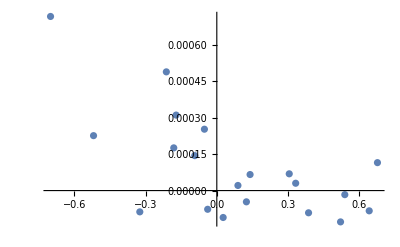

```mathematica
Show[ListPlot[temp2],Plot[x,{x,0.4,0.5}]]
```

## Individual-Based Simulations

Choosing parameters

## Choosing Parameters

### Randomly drawing parameters across parameter space

Fixing Host Population sizes equal to parasite population size

```mathematica
HtotEco=Sum[h[i,t],{i,1,2}]/.βSub/.equiEnd//Simplify
```

(2 γ κ)/(X+Y)

```mathematica
PtotEco=Sum[p[i,t],{i,1,2}]/.βSub/.equiEnd//Simplify
```

(2 (b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)

```mathematica
bSub=Flatten[Solve[HtotEco==PtotEco,b]]
```

{b→((X+Y) (α γ+δ))/(X+Y-2 γ)}

Stability criteria for γ.  γ<γCrit

```mathematica
γCrit=((X+Y) (b-δ))/(2 b);
```

```mathematica
Clear[randPars]
randPars[npts_]:=randPars[npts]=Block[{ct,Xr,Yr,br,γr,δr,αr,temp,out},out={};
For[ct=1,ct≤npts,ct++,
Xr=RandomReal[{0,1}];Yr=RandomReal[{0,Xr}];(*(*Neutral*)Yr=Xr;*)
αr=RandomReal[{0,1}];δr=RandomReal[{0.1,1}];γr=RandomReal[{0.1,1}];
temp={X->Xr,Y->Yr,α->αr,δ->δr,γ->γr};
br=b/.bSub/.temp;
temp={X->Xr,Y->Yr,b->br,α->αr,δ->δr,γ->γr};
If[γr<(γCrit/.temp)&&δr<br,
AppendTo[out,temp],ct--]
];
out
]
```

### Equating to epidemiological model

Setting Host Population Size to fH κ where fH is some constant between 0 and 1.

```mathematica
HtotEco=Sum[h[i,t],{i,1,2}]/.βSub/.equiEnd//Simplify
```

(2 γ κ)/(X+Y)

```mathematica
γSub[fH_]:=Flatten[Solve[HtotEco==fH κ,γ]]
```

```mathematica
γSub[fH]
```

{γ→1/2 fH (X+Y)}

Eliminate the effect of perturbations δ fH=γ fP

```mathematica
Clear[δSub]
δSub[fH_,fP_]:=Flatten[Solve[δ fH==(γ fP/.γSub[fH]),δ]]
```

```mathematica
δSub[fH,fP]
```

{δ→1/2 fP (X+Y)}

Setting αEco=αEpi/(αEpi+δEpi)

Setting the pathogen population size to fP κ where fP is some constant between 0 and 1.

```mathematica
Clear[PtotEco]
```

```mathematica
PtotEco[fH_,fP_]:=Sum[p[i,t],{i,1,2}]/.βSub/.equiEnd/.γSub[fH]/.δSub[fH,fP]/.α->α/(α+δ)//Simplify
```

```mathematica
Clear[bSub]
bSub[fH_,fP_]:=Solve[PtotEco[fH,fP]==fP κ,b]//FullSimplify//Flatten
```

```mathematica
bSub[fH,fP]
```

{b→-(fP (X+Y) (2 α+δ))/(2 (-1+fH) (α+δ))}

Stability criteria: γ<γCrit

```mathematica
γCrit=((X+Y) (b-δ))/(2 b);
```

```mathematica
γSub[fH]
```

{γ→1/2 fH (X+Y)}

```mathematica
γCrit/.δSub[fH,fP]
```

((X+Y) (b-1/2 fP (X+Y)))/(2 b)

```mathematica
Reduce[{(γ/.γSub[fH])<γCrit/.δSub[fH,fP],0<b,0<Y<X<1,0<fP<fH<1,0<α},α]//Simplify
```

0<Y<1&&Y<X<1&&0<fH<1&&0<fP<fH&&b>-(fP (X+Y))/(2 (-1+fH))&&α>0

System is always stable

#### Drawing Parameters

```mathematica
equiEnd
```

{h[1,t]→(γ κ)/(X+Y),h[2,t]→(γ κ)/(X+Y),p[1,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α),p[2,t]→((b (X+Y-2 γ)-(X+Y) δ) κ)/((X+Y)^2 α)}

```mathematica
Clear[randPars2Eco]
randPars2Eco[epiPars_]:=randPars2Eco[epiPars]=Block[{ct,Xr,Yr,br,γr,δr,αr,temp,temp2,out,fHEpi,fPEpi},out={};
For[ct=1,ct≤Length[epiPars],ct++,
fHEpi=1/(2 b (X+Y))(b X+b Y-X α-Y α-X δ-Y δ+√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))))/.epiPars[[ct]];
fPEpi=-1/(2 b (X+Y))(-b X-b Y+4 b α+X α+Y α+4 b γ+4 b δ+X δ+Y δ-√((X+Y) (b^2 (X+Y)+(X+Y) (α+δ)^2-2 b (X (α+δ)+Y (α+δ)-4 α (α+γ+δ)))))/.epiPars[[ct]];
αr=α/(α+δ)/.epiPars[[ct]];
Xr=(X/.epiPars[[ct]]);Yr=(Y/.epiPars[[ct]]);
γr=γ/.γSub[fHEpi]/.epiPars[[ct]];
δr=δ/.δSub[fHEpi,fPEpi]/.epiPars[[ct]];
br=b/.bSub[fHEpi,fPEpi]/.epiPars[[ct]];
temp2={X->Xr,Y->Yr,b->br,α->αr,δ->δr,γ->γr};
temp={fH->Sum[h[i,t],{i,1,2}]/κ/.equiEnd/.temp2,fP->Sum[p[i,t],{i,1,2}]/κ/.equiEnd/.temp2,X->Xr,Y->Yr,b->br,α->αr,δ->δr,γ->γr};
(*AppendTo[out,temp];*)
If[γr<(γCrit/.temp)&&δr<br,
AppendTo[out,temp],ct--]
];
out
]
```

## Making Input files

```mathematica
epiPars=randPars2Epi[100];
```

Given the total desired host population size K solving for κ

```mathematica
κSol[K_,pars_]:=κ/.Flatten[Solve[(HtotEco/.pars)==K,κ]]
```

```mathematica
κSol[J,{}]
```

(J (X+Y))/(2 γ)

```mathematica
nRep=7;
nDemes=1000;
gmax=250;
(*sampFreq=1;*)
```

```mathematica
ecoFile[pars_]:=Block[{out,rep},
out="Input file for Ecological simulations

number of reps (nRep): "<> ToString[nRep]<>"
number of demes (nDemes): "<> ToString[nDemes]<>"
maximum number of generations (gmax): "<> ToString[gmax]<>"
host birth rate (b): "<> ToString[b/.pars]<>"
matching infection rate (X): "<> ToString[X/.pars]<>"
mismatching infection rate (Y): "<> ToString[Y/.pars]<>"
host natural death rate (delta): "<> ToString[δ/.pars]<>"
death probability (alpha): "<> ToString[α/.pars]<>"
pathogen death rate (gamma): "<>ToString[γ/.pars]<>"
carrying capacity (kappa): ";
For[rep=0,rep<nRep,rep++,out=out<>ToString[κSol[10^(2+0.25*rep),pars]]<>" "];
out
]
```

```mathematica
Do[Export[NotebookDirectory[]<>"/sims_11_1/inputEco_"<>ToString[i]<>".txt",ecoFile[randPars2Eco[epiPars][[i]]]],{i,1,100}]
```

Importing values

## Parameters and Data

```mathematica
(*Random Sampling*)
fileV=NotebookDirectory[]<>"sims_11_1/eco_11_3/runEco_";
fileV2=NotebookDirectory[]<>"sims_11_1/eco_11_3/";
nRuns=100;
```

```mathematica
(*Equivalent to Epidemiolgoical Model*)
(*fileV=NotebookDirectory[]<>"sims_11_1/eco_11_6/runEco_";
fileV2=NotebookDirectory[]<>"sims_11_1/eco_11_6/";*)
nRuns=100;
```

```mathematica
Clear[pars]
pars[file_,run_]:=pars[file,run]=Import[file<>ToString[run]<>"/out.csv"]
```

```mathematica
Clear[nReps,nDemes,gmax,b,X,Y,δ,α,γ,κ]
nReps[file_,run_]:=pars[file,run][[2,2]]
nDemes[file_,run_]:=pars[file,run][[3,2]]
gmax[file_,run_]:=pars[file,run][[4,2]]
b[file_,run_]:=pars[file,run][[5,2]]
X[file_,run_]:=pars[file,run][[6,2]]
Y[file_,run_]:=pars[file,run][[7,2]]
δ[file_,run_]:=pars[file,run][[8,2]]
α[file_,run_]:=pars[file,run][[9,2]]
γ[file_,run_]:=pars[file,run][[10,2]]
κ[file_,run_,rep_]:=pars[file,run][[11,1+rep]];
```

```mathematica
simPars[file_,run_,rep_]:={b->b[file,run],δ->δ[file,run],X->X[file,run],Y->Y[file,run],α->α[file,run],γ->γ[file,run], κ->κ[file,run,rep]};
```

```mathematica
Clear[time,state,stateN]
time[file_,run_,rep_]:=time[file,run,rep]=Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/time.csv"][[;;,;;-2]]
state[file_,run_,rep_]:=state[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,1,4}]//N
stateN[file_,run_,rep_]:=stateN[file,run,rep]=Table[Import[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[v]<>".csv"][[;;,;;-2]],{v,5,8}]//N
```

```mathematica
Clear[MoranNeut]
MoranNeut[file_,run_,rep_]:=MoranNeut[file,run,rep]=Table[0.5(1-2/(h[1,t]+h[2,t]))^g,{g,1,gmax[file,run]}]/.equiEnd/.simPars[file,run,rep]
```

## Processing

### Bootstrap Functions

```mathematica
BootstrapMean[data_,nBoot_]:=BootstrapMean[data,nBoot]=Block[{out,b},out={};
For[b=1,b≤nBoot,b++,
AppendTo[out,Mean[RandomChoice[data,Length[data]]]]
];
out]
```

```mathematica
Bootstrap[data_,dummy_]:=Bootstrap[data,dummy]=RandomChoice[data,Length[data]]
```

### Allele Frequency

```mathematica
Clear[pHdeme,pHNdeme]
```

```mathematica
Clear[pHMtrx]
pHMtrx[file_,run_,rep_]:=pHMtrx[file,run,rep]=(state[file,run,rep][[1]])/(state[file,run,rep][[1]]+state[file,run,rep][[2]])//N
```

```mathematica
Clear[pHNMtrx]
pHNMtrx[file_,run_,rep_]:=pHNMtrx[file,run,rep]=(stateN[file,run,rep][[1]])/(stateN[file,run,rep][[1]]+stateN[file,run,rep][[2]])//N
```

### Heterozygosity Matrix

```mathematica
Clear[HetMtrx,HetMtrx2]
HetMtrx[file_,run_,rep_]:=HetMtrx[file,run,rep]=2pHMtrx[file,run,rep](1-pHMtrx[file,run,rep])
HetMtrx2[file_,run_,rep_]:=HetMtrx2[file,run,rep]=Table[HetMtrx[file,run,rep][[;;,g]]/.Indeterminate->0,{g,1,250}]//Transpose
```

```mathematica
Clear[HetNMtrx,HetNMtrx2]
HetNMtrx[file_,run_,rep_]:=HetNMtrx[file,run,rep]=2pHNMtrx[file,run,rep](1-pHNMtrx[file,run,rep])
HetNMtrx2[file_,run_,rep_]:=HetNMtrx2[file,run,rep]=Table[HetNMtrx[file,run,rep][[;;,g]]/.Indeterminate->MoranNeut[file,run,rep][[g]],{g,1,250}]//Transpose
```

### Heterozygosity at generation τ

```mathematica
Clear[HetCompMtrx2]
HetCompMtrx2[file_,rep_,τ_]:=HetCompMtrx2[file,rep,τ]=Import[fileV2<>"/HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv"]
```

### Harmonic Mean Population Size

```mathematica
Clear[NeMtrx]
NeMtrx[rep_]:=NeMtrx[rep]=Import[fileV2<>"/NeMtrx/NeMtrx_"<>ToString[rep]<>".csv"]
```

```mathematica
Clear[NeMtrx2]
NeMtrx2[rep_,g_]:=NeMtrx2[rep,g]=Import[fileV2<>"/NeMtrx/NeMtrx_"<>ToString[rep]<>"_"<>ToString[g]<>".csv"]
```

Processing (Run Only Once)

### Preprocessing- RUN ONLY ONCE!

```mathematica
Clear[HetCompMtrx]
HetCompMtrx[file_,rep_,τ_]:=Table[{Mean[HetNMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetNMtrx2[file,run,rep][[;;,τ]],1000]],Mean[HetMtrx2[file,run,rep][[;;,τ]]],StandardDeviation[BootstrapMean[HetMtrx2[file,run,rep][[;;,τ]],1000]]},{run,1,100}]
```

```mathematica
(*Run This Only Once*)
(*CreateDirectory[fileV2<>"HetMtrx"];*)
Table[Export[fileV2<>"HetMtrx/HetMtrx_"<>ToString[rep]<>"_"<>ToString[τ]<>".csv",HetCompMtrx[fileV,rep,τ]],{rep,1,7},{τ,10,250,10}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Harmonic Mean Population Size

```mathematica
Clear[HarmonicMeanNe]
HarmonicMeanNe[file_,run_,rep_,g_]:=HarmonicMeanNe[file,run,rep]=Block[{temp},temp=Total[state[file,run,rep][[{1,2},;;,;;g]]];
Map[If[Min[#]==0,0,g/Total[#^-1]]&,temp]]
```

```mathematica
NeExp[gen_]:=Do[Export[fileV2<>"NeMtrx/NeMtrx_"<>ToString[rep]<>"_"<>ToString[gen]<>".csv",Table[HarmonicMeanNe[fileV,run,rep,gen],{run,1,100}]];Print[rep],{rep,1,7}];
```

```mathematica
(*Run This Only Once*)
(*CreateDirectory[fileE2<>"NeMtrx"];*)
NeExp[20]
```

1

2

3

4

5

6

7

```mathematica
NeExp[10]
```

1

2

3

4

5

6

7

```mathematica
NeExp[50]
```

1

2

3

4

5

6

7

```mathematica
NeExp[250]
```

1

2

3

4

5

6

7

Plotting

## Dynamics of a single rep

```mathematica
dynPlot[file_,run_,rep_]:=Show[
(*Neutral Simulations*)
ListLinePlot[{Mean[HetNMtrx[file,run,rep]],Mean[HetNMtrx[file,run,rep]]+2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetNMtrx[file,run,rep]]-2 StandardDeviation[HetNMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Black,Gray,Gray},Filling->2->{3},FillingStyle->Directive[Gray,Opacity[0.2]]],
(*Coevolutionary Simulations*)
(*ListLinePlot[Table[Mean[Bootstrap[Htable[file,run,rep],bs]],{bs,0,100}],PlotStyle->Directive[Pink,Opacity[0.1]]],*)ListLinePlot[{Mean[HetMtrx[file,run,rep]],Mean[HetMtrx[file,run,rep]]+2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]],Mean[HetMtrx[file,run,rep]]-2 StandardDeviation[HetMtrx[file,run,rep]]/Sqrt[nDemes[file,run]]},PlotStyle->{Red,Pink,Pink},Filling->2->{3},FillingStyle->Directive[Pink,Opacity[0.2]]],
(*Moran Neutral Expectation*)
ListLinePlot[MoranNeut[file,run,rep],PlotStyle->Purple](*,PlotRange->{{0,5},{0.48,0.5}}*)]
```

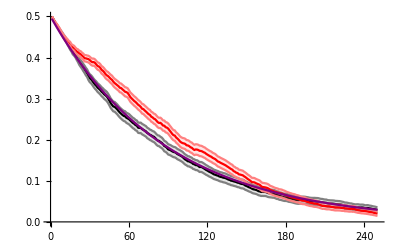

```mathematica
dynPlot[fileV,8,2]
```

## Heterozygosity Across Parameter Space

### Mean Smoothing

Project data onto the X=Y line.

```mathematica
Clear[dataNew]
dataNew[data_]:=dataNew[data]=Transpose[{Cos[Abs[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]]*Sqrt[Total[Transpose[data^2]]],Sin[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]*Sqrt[Total[Transpose[data^2]]]}]
```

A gaussian weighting of the data  near the point xNew along the X=Y line

```mathematica
Clear[weights]
weights[xNew_,αW_,data_]:=weights[xNew,αW,data]=Exp[-(dataNew[data][[;;,1]]-xNew)^2/(2 αW^2)]//Chop;
```

Find the weighted mean and standard deviation and standard error.

```mathematica
Clear[meanNew]
meanNew[xNew_,αW_,data_]:=meanNew[xNew,αW,data]=Total[weights[xNew,αW,data]dataNew[data][[;;,2]]]/Total[weights[xNew,αW,data]]
```

```mathematica
SDNew[xNew_,αW_,data_]:=Sqrt[Total[weights[xNew,αW,data]*(dataNew[data][[;;,2]]-meanNew[xNew,αW,data])^2]/Total[weights[xNew,αW,data]]]
```

```mathematica
SENew[xNew_,αW_,data_]:=SDNew[xNew,αW,data]/Sqrt[Total[weights[xNew,αW,data]]]
```

The rolling average fit along the X+Y line (rotated plot)

```mathematica
Clear[RollFit]
RollFit[αW_,npts_,data_]:=RollFit[αW,npts,data]=Table[{x,meanNew[x,αW,data]},{x,0.001,Sqrt[2*0.5^2]-0.001,Sqrt[2*0.5^2]/npts}];
```

Projecting back into the original coordinates.

```mathematica
RollFitOld[αW_,npts_,data_]:=Transpose[{Cos[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2],Sin[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2]}]
```

### Variation within versus across replicates

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
VarVisual[rep_]:=Block[{temp},temp=Sort[Map[{#[[3]],1.96#[[4]]}&,HetCompMtrx2[fileV,rep,250]],#1[[1]]<#2[[1]]&];
ErrorListPlot[temp,PlotRange->{Min[Map[#[[1]]-#[[2]]&,temp]]0.95,Max[Map[#[[1]]+#[[2]]&,temp]]*1.05},Frame->True,FrameTicksStyle->Directive[Black,12],ImageSize->Medium,PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]]
```

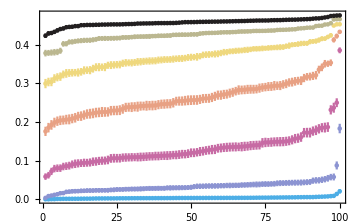

```mathematica
Show[Table[VarVisual[rep],{rep,1,7}],PlotRange->All]
(*Export[NotebookDirectory[]<>"Plots/Eco_Variation.pdf",%,ImageResolution->300];*)
```

```mathematica
VarWB=Table[{Round[Mean[HetCompMtrx2[fileV,rep,250][[;;,4]]],0.0001],Round[StandardDeviation[HetCompMtrx2[fileV,rep,250][[;;,3]]],0.001],Round[StandardDeviation[HetCompMtrx2[fileV,rep,250][[;;,3]]]/Mean[HetCompMtrx2[fileV,rep,250][[;;,4]]],0.01]},{rep,1,7}]
```

{{0.0011,0.003,2.27},{0.0034,0.019,5.62},{0.0057,0.043,7.5},{0.0059,0.048,8.11},{0.0043,0.032,7.41},{0.0027,0.017,6.47},{0.0017,0.009,5.6}}

```mathematica
Export[fileV2<>"VarWB.csv",VarWB]
```

/Users/ailenemacpherson/Desktop/EcoEpiDrift/sims_11_1/eco_11_3/VarWB.csv

```mathematica
ErrorListPlot2[file_,rep_,τ_]:=Block[{temp},
temp=Sort[HetCompMtrx2[file,rep,τ],#1[[3]]<#2[[3]]&];
Show[ListLinePlot[Table[{{r,temp[[r,3]]-2temp[[r,4]]},{r,temp[[r,3]]+2temp[[r,4]]}},{r,1,100}],PlotStyle->Directive[Lighter[ColorData["CMYKColors"][(rep-1)/6]]],PlotRange->{0,0.5}],
ListPlot[Table[{r,temp[[r,3]]},{r,1,100}],PlotStyle->ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{"●",4}]
]
]
```

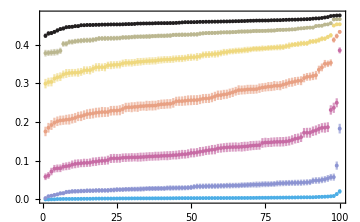

```mathematica
Show[Table[ErrorListPlot2[fileV,rep,250],{rep,1,7}],PlotRange->All,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
Export[NotebookDirectory[]<>"Plots/Eco_Variation.pdf",%,ImageResolution->300];
```

```mathematica
Clear[temp]
```

```mathematica
temp[file_,rep_,τ_]:=Sort[Table[{Quantile[HetMtrx[file,run,rep][[τ]],0.25],Quantile[HetMtrx[file,run,rep][[τ]],0.75],Mean[HetMtrx[file,run,rep][[τ]]]},{run,1,100}],#1[[3]]<#2[[3]]&];
```

Plot showing the 25th to 75th percentile.

```mathematica
ErrorListPlot3[file_,rep_,τ_]:=Block[{temp},
temp=Sort[Table[{Quantile[HetMtrx[file,run,rep][[τ]],0.25],Quantile[HetMtrx[file,run,rep][[τ]],0.75],Mean[HetMtrx[file,run,rep][[τ]]]},{run,1,100}],#1[[3]]<#2[[3]]&];
Show[ListLinePlot[Table[{{r,temp[[r,1]]},{r,temp[[r,2]]}},{r,1,100}],PlotStyle->Directive[Lighter[ColorData["CMYKColors"][(rep-1)/6]]],PlotRange->All],
ListPlot[Table[{r,temp[[r,3]]},{r,1,100}],PlotStyle->ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{"●",4}]
]
]
```

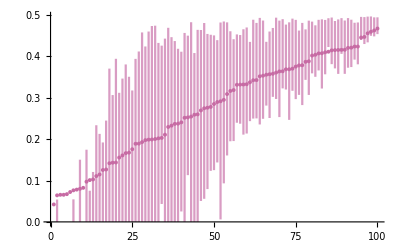

```mathematica
ErrorListPlot3[fileV,3,250]
```

### WF Diploid Over-dominance as a comparison

transition probability of i copies to j copies of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==0,If[j==0,1,0],If[i==n,If[j==n,1,0],Binomial[ n,j]((i/n (1+w[i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^j(((n-i)/n (1+w[n-i,n,s]))/(i/n (1+w[i,n,s])+(n-i)/n (1+w[n-i,n,s])))^(n-j)]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t].p0Vec[n]
```

```mathematica
pOut[Round[10^2.5,2],0.01,250]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hOver[Round[10^2.75,2],0.01,250]
```

0.443671

```mathematica
hNeut[n_,t_]:=1/2 Exp[-t/n]
```

```mathematica
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],0.01,250]},{npower,2,2.75,0.25}]
```

{{1/(2 ⅇ^(5/2)),0.0899257},{1/(2 ⅇ^(125/89)),0.239548},{1/(2 ⅇ^(125/158)),0.374202},{1/(2 ⅇ^(125/281)),0.443671}}

```mathematica
temp={{1/(2 ⅇ^(5/2)),0.08992571775402472},{1/(2 ⅇ^(125/89)),0.23954849222376998},{1/(2 ⅇ^(125/158)),0.3742022797759149},{1/(2 ⅇ^(125/281)),0.443671355336855}};
```

```mathematica
HetOver=Join[{{0,0}},temp,{{0.5,0.5}}]//N;
```

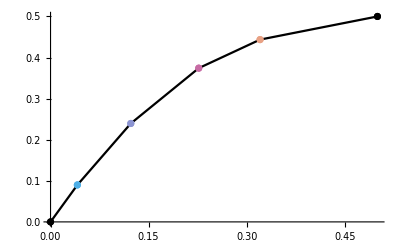

```mathematica
Show[ListLinePlot[HetOver,PlotStyle->Black],ListPlot[Map[{#}&,HetOver],PlotStyle->Join[{Black},Table[ ColorData["CMYKColors"][(rep-1)/6],{rep,1,4}],{Black}]]]
```

### Moran Diploid Over-dominance as a comparison

transition probability of i copies to j copies (out of n total copies) of the allele

```mathematica
w[i_,n_,s_]:=(i/n)(1-s)+(n-i)/n-((n-i)/n(1-s)+i/n)//Simplify
```

```mathematica
wA[i_,n_,s_]:=((i/n)(1-s)+(n-i)/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
wa[i_,n_,s_]:=((n-i)/n(1-s)+i/n)/((i/n)^2(1-s)+2 i/n(n-i)/n+((n-i)/n)^2(1-s))
```

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(w[p[t]n,n,s])p[t](1-p[t])/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
npSol=Flatten[NDSolve[{D[p[t],t]==(wA[p[t]n,n,s]-1)p[t]/.{n->100,s->0.1},p[0]==0.1},p[t],{t,0,100}]]
```

{p[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}

```mathematica
p[i_,j_,n_,s_]:=If[i==j,1-wA[i,n,s] i/n(n-i)/n-wa[i,n,s](n-i)/n i/n,If[j==i+1,wA[i,n,s] i/n(n-i)/n,If[j==i-1,wa[i,n,s](n-i)/n i/n,0]]]
```

```mathematica
p0Vec[n_]:=Table[If[i==n/2,1,0],{i,0,n}]
```

```mathematica
Clear[tMtrx]
tMtrx[n_,s_]:=tMtrx[n,s]=Table[p[i,j,n,s],{j,0,n},{i,0,n}]
```

```mathematica
Clear[pOut]
pOut[n_,s_,t_]:=pOut[n,s,t]=MatrixPower[tMtrx[n,s],t n].p0Vec[n]
```

```mathematica
hOver[n_,s_,t_]:=Table[2 i/n((n-i)/n),{i,0,n}].pOut[n,s,t]
```

```mathematica
hNeut[n_,t_]:=1/2 (1-2/n)^t//N
```

```mathematica
Clear[HetOver]
HetOver[s_,τ_]:=HetOver[s,τ]=Block[{temp},
temp=Table[{hNeut[Round[10^npower,2],250],hOver[Round[10^npower,2],s,τ]},{npower,2,3.25,0.25}];
Join[{{0,0}},temp,{{0.5,0.5}}]//N]
```

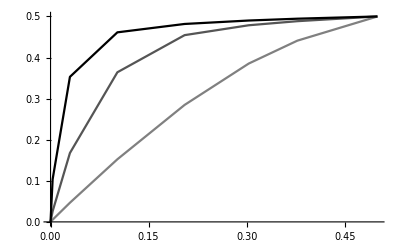

```mathematica
ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}]
```

### Comparison to the simulated neutral expectation

```mathematica
meanPlot[file_,τ_]:=Block[{sigData,meanData},
meanData=Flatten[Table[HetCompMtrx2[file,rep,τ][[;;,{1,3}]],{rep,1,7}],1];
sigData[rep_]:=sigData[rep]=Select[HetCompMtrx2[file,rep,τ],(#[[3]]-2 #[[4]])>(#[[1]]+2#[[2]])||(#[[3]]+2 #[[4]])<(#[[1]]-2#[[2]])&];
Show[
Table[
ListPlot[{sigData[rep][[;;,{1,3}]],Complement[HetCompMtrx2[file,rep,τ],sigData[rep]][[;;,{1,3}]]},PlotStyle-> ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{●,○}],{rep,1,7}],
(*Mean Fit and bootstrap samples*)
ListLinePlot[Table[RollFitOld[0.05,40,Bootstrap[meanData,x]],{x,1,100}],PlotStyle->Directive[Green(*Lighter[RGBColor[{241/255,157/255,25/255}]]*),Opacity[0.1]]],
ListLinePlot[RollFitOld[0.05,40,meanData],PlotStyle->Darker[Green](*RGBColor[{241/255,157/255,25/255}]*)],Plot[x,{x,0,0.5},PlotStyle->{Black,Thick,Dashing[0.02]}],
(*Comparison to Overdominance*)
ListLinePlot[{HetOver[0.01,250],HetOver[0.05,250],HetOver[0.1,250]},PlotStyle->{Gray,Darker[Gray],Black}],
(*Plot Options*)
PlotRange->{{0,0.5},{0,0.5}},AspectRatio->1,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],Axes->False]]
```

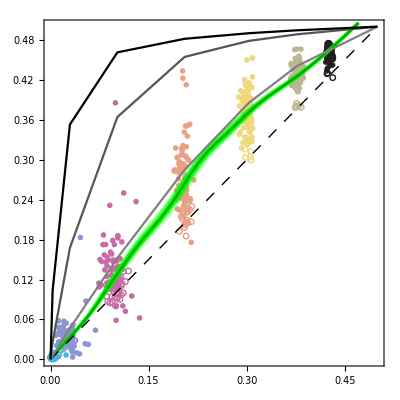

```mathematica
meanPlot[fileV,250]
Export[NotebookDirectory[]<>"Plots/Eco_MeanHet_Rand2.pdf",%,ImageResolution->300];
```

```mathematica
meanData[file_,τ_]:=Flatten[Table[HetCompMtrx2[file,rep,τ][[;;,{1,3}]],{rep,1,7}],1];
```

```mathematica
meanExport[file_,τ_]:=Transpose[Flatten[Join[{Transpose[RollFitOld[0.1,50,meanData[file,τ]]]},Table[Transpose[RollFitOld[0.1,50,Bootstrap[meanData[file,τ],x]]],{x,1,100}]],1]]
```

```mathematica
Export[fileV2<>"MeanHet.csv",meanExport[fileV,250]];
```

```mathematica
KLeg=PointLegend[Table[ColorData["CMYKColors"][rep/6],{rep,0,6}],Table[ToString[Round[10^(2+0.25rep)]],{rep,0,6}],LegendFunction->"Frame",LegendLabel->Text[Style["K",14,Bold]],LegendMarkerSize->15]
Export[NotebookDirectory[]<>"Plots/KLeg.pdf",KLeg];
```

### Comparison to the Moran neutral expectation

```mathematica
meanPlot2[file_,τ_]:=Block[{tempMtrx,sigData,meanData},
tempMtrx[rep_]:=tempMtrx[rep]=Join[{Table[MoranNeut[file,run,rep][[τ]],{run,1,100}]},{Table[0,{run,1,100}]},Transpose[HetCompMtrx2[file,rep,τ][[;;,{3,4}]]]]//Transpose;
meanData=Flatten[Table[tempMtrx[rep][[;;,{1,3}]],{rep,1,7}],1];
sigData[rep_]:=sigData[rep]=Select[tempMtrx[rep],(#[[3]]-2 #[[4]])>(#[[1]]+2#[[2]])||(#[[3]]+2 #[[4]])<(#[[1]]-2#[[2]])&];
Show[
Table[
ListPlot[{sigData[rep][[;;,{1,3}]],Complement[tempMtrx[rep],sigData[rep]][[;;,{1,3}]]},PlotStyle-> ColorData["CMYKColors"][(rep-1)/6],PlotMarkers->{●,○}],{rep,1,7}],
ListLinePlot[Table[RollFitOld[0.05,40,Bootstrap[meanData,x]],{x,1,100}],PlotStyle->Directive[Green,Opacity[0.1]]],
ListLinePlot[RollFitOld[0.05,40,meanData],PlotStyle->Darker[Green]],Plot[x,{x,0,0.5},PlotStyle->{Black,Thick,Dashed}],PlotRange->{{0,0.5},{0,0.5}},Frame->True,FrameTicksStyle->Directive[Black,12],AspectRatio->1]]
```

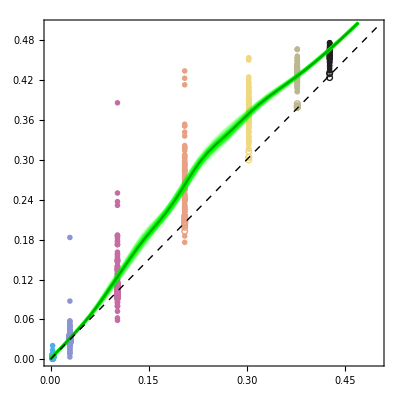

```mathematica
meanPlot2[fileV,250]
Export[NotebookDirectory[]<>"Plots/Eco_MeanHet_Moran_Rand.pdf",%,ImageResolution->300];
```

```mathematica
meanPlot3[file_,τ_]:=Block[{tempMtrx,sigData,meanData},
tempMtrx[rep_]:=tempMtrx[rep]=Join[{Table[MoranNeut[file,run,rep][[τ]],{run,1,100}]},{Table[0,{run,1,100}]},Transpose[HetCompMtrx2[file,rep,τ][[;;,{3,4}]]]]//Transpose;
Show[ListPlot[Table[Transpose[{Table[RandomReal[{-0.01+rep,0.01+rep}],{run,1,nRuns}],tempMtrx[rep][[;;,3]]-tempMtrx[rep][[;;,1]]}],{rep,1,7}],PlotStyle->Table[ ColorData["CMYKColors"][(rep-1)/6],{rep,1,7}],PlotMarkers->●,PlotRange->{{0,8},{-0.25,0.3}},Axes->False,Frame->True],Plot[0,{x,0,8},PlotStyle->{Black,Dashed}]]
]
```

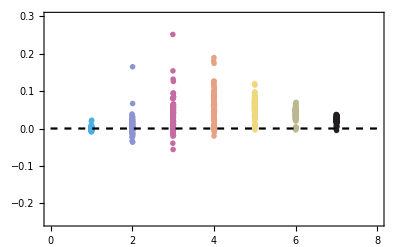

```mathematica
meanPlot3[fileV,200]
```

### Explaining Variation

#### Perturbations

```mathematica
γδPlot[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Transpose[{Table[δ[file,run]-γ[file,run],{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Table[R2[rep]=lm[data[rep],"RSquared"],{rep,1,7}];
Table[Slope[rep]={lm[data[rep],"BestFitParameters"][[2]],lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]-lm[data[rep],"BestFitParameters"][[2]]},{rep,1,7}];
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16],ImageSize->Medium]
]
```

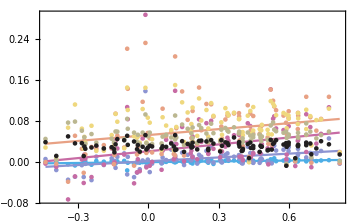

```mathematica
γδPlot[fileV,250]
Export[NotebookDirectory[]<>"Plots/Eco_Pert.pdf",%,ImageResolution->300];
```

```mathematica
Table[Join[Round[{R2[rep]},0.01],Round[Slope[rep],0.001]],{rep,1,7}]
Export[NotebookDirectory[]<>"RSquaredTemp.csv",%];
```

{{0.25,0.005,0.002},{0.14,0.025,0.012},{0.1,0.044,0.027},{0.06,0.038,0.03},{0.04,0.019,0.02},{0.,-0.003,0.011},{0.01,-0.003,0.006}}

#### Stabilizing Effect

```mathematica
rFit[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Map[If[#[[1]]>0,{Log[#[[1]]],#[[2]]},{0,#[[2]]}]&,Transpose[{Table[-r/.nlFitPars[file,run,rep],{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}]];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],(*Print[lm[data[rep],"RSquared"]];*)Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Table[R2[rep]=lm[data[rep],"RSquared"],{rep,1,7}];
Table[Slope[rep]={lm[data[rep],"BestFitParameters"][[2]],lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]-lm[data[rep],"BestFitParameters"][[2]]},{rep,1,7}];
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,Axes->False,Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,16]]
]
```

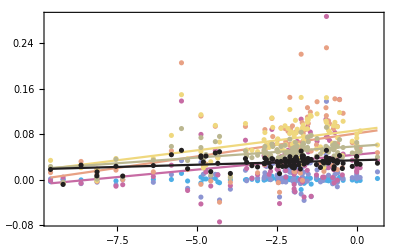

```mathematica
rFit[fileV,250]
Export[NotebookDirectory[]<>"Plots/Eco_r.pdf",%,ImageResolution->300];
```

```mathematica
Table[Join[Round[{R2[rep]},0.01],Round[Slope[rep],0.001]],{rep,1,7}]
Export[NotebookDirectory[]<>"RSquaredTemp.csv",%];
```

{{0.,0.,0.},{0.03,0.002,0.002},{0.06,0.005,0.004},{0.12,0.008,0.004},{0.21,0.007,0.003},{0.23,0.004,0.001},{0.12,0.002,0.001}}

#### Harmonic Mean Population Size

Comparison to the NEUTRAL MORAN MODEL

```mathematica
Does the harmonic mean at time g explain ΔH at time t
```

```mathematica
Clear[NePlot1]
```

```mathematica
NePlot1[file_,τ_,g_]:=Block[{eqTab,data,plot,min,max,lm},
eqTab[rep_]:=Table[Sum[h[i,t],{i,1,2}]/.equiEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=Transpose[{(Mean[Transpose[NeMtrx2[rep,g]]]-eqTab[rep])/eqTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-Table[MoranNeut[file,run,rep][[g]],{run,1,100}]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y,ConfidenceLevel->.99][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*Storing Fit Info*)
FitTab1[τ,g]=Table[Flatten[{StandardDeviation[data[rep][[;;,1]]],lm[data[rep],"BestFitParameters"],lm[data[rep],"ParameterConfidenceIntervals"],lm[data[rep],"RSquared"]}],{rep,1,7}];
(*Plotting*)
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

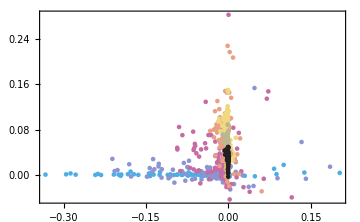

```mathematica
NePlot1[fileV,250,250]
```

```mathematica
FitTab1[250,250]
```

{{0.0893773,0.000753627,0.00413153,-0.0000789117,0.00158617,-0.00349828,0.0117613,0.0202297},{0.0659756,0.00469664,0.00507276,-0.00112292,0.0105162,-0.0719346,0.0820801,0.000305466},{0.0335737,0.0248515,-0.135536,0.0123314,0.0373717,-0.472901,0.201828,0.0112377},{0.011514,0.0550062,-0.908425,0.0415451,0.0684673,-1.98173,0.164876,0.0480212},{0.00378682,0.0613775,-2.25906,0.0517991,0.0709559,-4.41101,-0.107106,0.0720117},{0.0017834,0.0447127,-2.79691,0.0388685,0.0505569,-5.29101,-0.302808,0.0813487},{0.00106006,0.0278592,-2.87973,0.0247451,0.0309734,-5.08039,-0.679077,0.107604}}

Comparison to the Simulated Neutral Expectation

Does the harmonic mean at time g explain ΔH at time t

```mathematica
Clear[FitTab2]
```

```mathematica
NePlot2[file_,τ_,g_]:=Block[{eqTab,data,plot,min,max,lm},
eqTab[rep_]:=Table[Sum[h[i,t],{i,1,2}]/.equiEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_]:=Transpose[{(Mean[Transpose[NeMtrx2[rep,g]]]-eqTab[rep])/eqTab[rep],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min[rep_]:=Min[data[rep][[;;,1]]];max[rep_]:=Max[data[rep][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y,ConfidenceLevel->.99][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min[rep],max[rep]},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
(*Storing Fit Info*)
FitTab2[τ,g]=Table[Flatten[{StandardDeviation[data[rep][[;;,1]]],lm[data[rep],"BestFitParameters"],lm[data[rep],"ParameterConfidenceIntervals"],lm[data[rep],"RSquared"]}],{rep,1,7}];
(*Plotting*)
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameTicksStyle->Directive[Black,12], ImageSize->Medium]
]
```

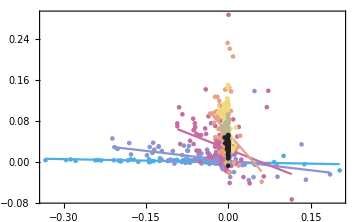

```mathematica
NePlot2[fileV,250,250]
Export[NotebookDirectory[]<>"Plots/Eco_Ne.pdf",%,ImageResolution->300];
```

```mathematica
Round[FitTab2[250,250],0.001]//MatrixForm
```

(0.089 | -0.001 | -0.02 | -0.002 | 0. | -0.028 | -0.012 | 0.293
0.066 | 0.002 | -0.126 | -0.004 | 0.008 | -0.201 | -0.051 | 0.166
0.034 | 0.024 | -0.422 | 0.012 | 0.037 | -0.76 | -0.084 | 0.099
0.012 | 0.055 | -1.222 | 0.041 | 0.068 | -2.305 | -0.139 | 0.082
0.004 | 0.063 | -2.606 | 0.053 | 0.072 | -4.767 | -0.444 | 0.093
0.002 | 0.045 | -2.712 | 0.039 | 0.051 | -5.261 | -0.163 | 0.074
0.001 | 0.027 | -3.173 | 0.024 | 0.031 | -5.475 | -0.871 | 0.118)

```mathematica
LatexExport[tab_]:=Block[{out,r},out="";
For[r=1,r≤7,r++,
out=out<>"\("<>ToString[2+(r-1)0.25]<>"\)&\("<>ToString[tab[[r,1]]]<>"\)&\("<>ToString[tab[[r,2]]]<>"\\pm "<>ToString[tab[[r,5]]-tab[[r,2]]]<>"\)&\("<>ToString[tab[[r,3]]]<>"\\pm "<>ToString[tab[[r,7]]-tab[[r,3]]]<>"\)&\("<>ToString[tab[[r,8]]]<>"\)\\"<>"\\"<>"\n"
];
out
]
```

```mathematica
LatexExport[Round[FitTab2[250,250],0.001]]
```

\(2.\)&\(0.089\)&\(-0.001\pm 0.001\)&\(-0.02\pm 0.008\)&\(0.293\)\\
\(2.25\)&\(0.066\)&\(0.002\pm 0.006\)&\(-0.126\pm 0.075\)&\(0.166\)\\
\(2.5\)&\(0.034\)&\(0.024\pm 0.013\)&\(-0.422\pm 0.338\)&\(0.099\)\\
\(2.75\)&\(0.012\)&\(0.055\pm 0.013\)&\(-1.222\pm 1.083\)&\(0.082\)\\
\(3.\)&\(0.004\)&\(0.063\pm 0.009\)&\(-2.606\pm 2.162\)&\(0.093\)\\
\(3.25\)&\(0.002\)&\(0.045\pm 0.006\)&\(-2.712\pm 2.549\)&\(0.074\)\\
\(3.5\)&\(0.001\)&\(0.027\pm 0.004\)&\(-3.173\pm 2.302\)&\(0.118\)\\

```mathematica
Export[NotebookDirectory[]<>"NeFit.txt",LatexExport[Round[FitTab2[250,250],0.001]]];
```

Variation in Effective population size

```mathematica
eqTab[file_,rep_]:=Table[Sum[h[i,t],{i,1,2}]/.equiEnd/.simPars[file,run,rep],{run,1,100}];
data[rep_,τ_,g_]:=Transpose[{eqTab[fileV,rep],Mean[Transpose[NeMtrx2[rep,g]]]}]
```

```mathematica
PerVar[rep_,τ_,g_]:=Round[StandardDeviation[data[rep,τ,g][[;;,2]]/data[rep,τ,g][[1,1]]],0.001]
```

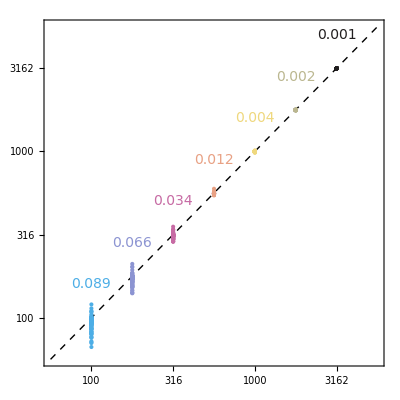

```mathematica
Show[Plot[x,{x,1.75,3.75},PlotStyle->Directive[Thin,Black,Dashed]],ListPlot[Table[Log10[data[rep,250,250]],{rep,1,7}],PlotStyle->Table[ColorData["CMYKColors"][(rep-1)/6],{rep,1,7}]],AspectRatio->1,Frame->True,PlotRange->{{1.75,3.75},{1.75,3.75}},FrameTicks->{{Table[{c,Round[10^c]},{c,2,4,0.5}],False},{Table[{c,Round[10^c]},{c,2,4,0.5}],False}},FrameTicksStyle->Directive[Black,14],Axes->False,Epilog->Table[Text[Style[ToString[PerVar[rep,250,250]],14,ColorData["CMYKColors"][(rep-1)/6]],{2+0.25 (rep-1),2+0.25 (rep-1)+0.2}(*Scaled[{0.1,0.1+(0.6-0.1)/7(6-rep)}]*)],{rep,1,7}] ]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/NeVar.pdf",%,ImageResolution->300]
```

/Users/ailenemacpherson/Documents/UBC/Warwick/EcoEpiDrift/Plots/NeVar.pdf

#### Non-leading Eigenvalue

```mathematica
λN[file_,run_,rep_]:=(-b γ+√(γ (-b (X+Y) (X+Y-2 γ)+b^2 γ+(X+Y)^2 δ)))/(X+Y)/.simPars[file,run,rep]
```

```mathematica
λNPlot[file_,τ_]:=Block[{data,plot,min,max,lm},
data[rep_]:=Transpose[{Table[Re[λN[file,run,rep]](*(X[file,run]-Y[file,run])*),{run,1,nRuns}],HetCompMtrx2[file,rep,τ][[;;,3]]-HetCompMtrx2[file,rep,τ][[;;,1]]}];
min=Min[data[1][[;;,1]]];max=Max[data[1][[;;,1]]];
lm[data_,x_]:=LinearModelFit[data,y,y][x];
plot[rep_]:=If[Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,1]]]==Sign[lm[data[rep],"ParameterConfidenceIntervals"][[2,2]]],Print[lm[data[rep],"RSquared"]];Show[ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],Plot[lm[data[rep],ξ],{ξ,min,max},PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]],ListPlot[data[rep],PlotStyle->ColorData["CMYKColors"][(rep-1)/6]]
];
Show[Table[plot[rep],{rep,1,7}],PlotRange->All,AxesOrigin->{0,0},Frame->True,FrameLabel->{"λN","ΔH"},ImageSize->Large]
]
```

0.124772

0.0959366

0.0424136

0.00544998

0.0183326

0.00245724

0.0145605

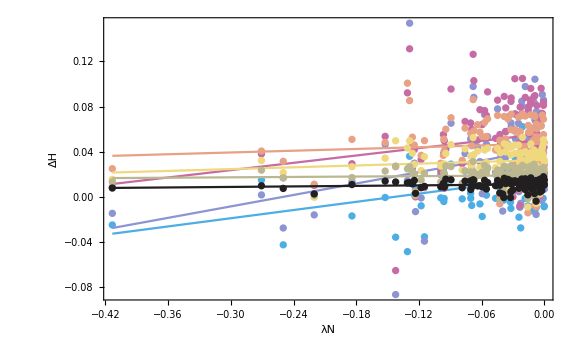

```mathematica
λNPlot[fileV,100]
```

## Allele Frequency Dynamics

```mathematica
(*The really small element of rep=3*)
Ordering[HetCompMtrx2[fileV,3,200][[;;,3]],3]
```

{79,66,92}

```mathematica
(*The really high element of rep=3*)
Ordering[HetCompMtrx2[fileV,3,200][[;;,3]],-1]
```

{46}

```mathematica
AFPlot[file_,run_,rep_,nd_]:=Block[{h1,h2,p1,p2,coev,dirSel,fixed,extinct,all},
{h1,h2,p1,p2}=SparseArray[state[file,run,rep][[;;,1;;nd,;;]]];
all=Flatten[Table[{deme,g},{deme,1,nd},{g,1,250}],1];
coev=Intersection[h1["NonzeroPositions"],h2["NonzeroPositions"],p1["NonzeroPositions"],p2["NonzeroPositions"]];
fixed=Union[Complement[all,h1["NonzeroPositions"]],Complement[all,h2["NonzeroPositions"]]];
extinct=Complement[Intersection[Complement[all,p1["NonzeroPositions"]],Complement[all,p2["NonzeroPositions"]]],fixed];
dirSel=Complement[Union[Complement[p1["NonzeroPositions"],p2["NonzeroPositions"]],Complement[p2["NonzeroPositions"],p1["NonzeroPositions"]]],Union[fixed,extinct]];
coev=Table[Select[coev,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];dirSel=Table[Select[dirSel,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];fixed=Table[Select[fixed,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];
extinct=Table[Select[extinct,#[[1]]==d&],{d,1,nd}][[;;,;;,2]];

Show[ListLinePlot[Table[pHMtrx[file,run,rep][[d,coev[[d]]]],{d,1,nd}],PlotStyle->Directive[Gray,Opacity[0.2]]],ListLinePlot[Table[If[Length[dirSel[[d]]]>0,Transpose[{dirSel[[d]],pHMtrx[file,run,rep][[d,dirSel[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Red,Opacity[0.3]]],ListLinePlot[Table[If[Length[extinct[[d]]]>0,Transpose[{extinct[[d]],pHMtrx[file,run,rep][[d,extinct[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Green,Opacity[0.3]]],ListLinePlot[Table[If[Length[fixed[[d]]]>0,Transpose[{fixed[[d]],pHMtrx[file,run,rep][[d,fixed[[d]]]]}],Missing[]],{d,1,nd}],PlotStyle->Directive[Blue,Opacity[0.2]]],Frame->True]
]
```

```mathematica
Clear[h1,h2,p1,p2]
```

```mathematica
(*The really small element of rep=3*)
low[rep_]:=Ordering[HetCompMtrx2[fileV,rep,200][[;;,3]],3]
(*The really high element of rep=3*)
high[rep_]:=Ordering[HetCompMtrx2[fileV,rep,200][[;;,3]],-3]
AFGrid[rep_]:=GraphicsGrid[{Table[AFPlot[fileV,low[rep][[run]],rep,100],{run,1,3}],Table[AFPlot[fileV,high[rep][[run]],rep,100],{run,1,3}]},ImageSize->Full]
```

```mathematica
AFGrid[3]
```

-Graphics-

## Fixation Order

```mathematica
hostFixTime[file_,run_,rep_]:=Table[FirstPosition[state[file,run,rep][[{1,2},d,;;]],0.],{d,1,1000}]
```

```mathematica
pathFixTime[file_,run_,rep_]:=Table[FirstPosition[state[file,run,rep][[{3,4},d,;;]],0.],{d,1,1000}]
```

```mathematica
pathExtinctTime[file_,run_,rep_]:=Table[FirstPosition[Total[state[file,run,rep][[{3,4},d,;;]]],0.],{d,1,1000}]
```

```mathematica
Clear[fixOrder]
fixOrder[file_,rep_]:=fixOrder[file,rep]=Block[{temp1,temp2,temp3,temp4,temp5,run,out},out={};
For[run=1,run≤100,run++,
(*All Data Points*)
temp1=Transpose[{hostFixTime[file,run,rep],pathFixTime[file,run,rep],pathExtinctTime[file,run,rep]}];
(*Host Fixed*)
temp2=DeleteCases[temp1,_?(#[[1]]==Missing["NotFound"]&)];
(*Host Fixed and Pathogen Fixed*)
temp3=DeleteCases[temp2,_?(#[[2]]==Missing["NotFound"]&)];
(*Pathogen Fixed (Pathogen may have gone extict) then Host fixed*)
temp4=Select[temp3,#[[1,2]]>#[[2,2]]&];
(*Pathogen Fixed, Pathogen Extinct, then Host fixed*)
temp5=Select[temp4,#[[1,2]]>#[[3,1]]&];
AppendTo[out,{Length[temp1]-Length[temp2](*Host Polymorphic*),Length[temp2]-Length[temp3](*Host Fixed, Pathogen Polymorphic*),Length[temp3]-Length[temp4](*Host Fixed First*),Length[temp4]-Length[temp5](*Pathogen Fixed then Host Fixed*),Length[temp5](*Pathogen Fixed then Pathogen Extinct, then Host Fixed*)}];
];
out/nRuns
]
```

```mathematica
fixBarChart[file_,rep_,τ_]:=BarChart[fixOrder[file,rep][[Ordering[Table[α/.simPars[fileV,run,rep],{run,1,nRuns}]](*Ordering[HetCompMtrx2[file,rep,τ][[;;,3]]]*)]],ChartLayout->"Stacked",ChartStyle->{Gray,Blue,Blue,Red,Green},Frame->True,FrameTicks->{{True,False},{True,False}},ImageSize->Medium,FrameTicksStyle->Directive[Black,14]]
```

Gray= Host and pathogen polymorphic at generation 250
Blue= Host fixed before pathogen
Red= Pathogen  fixes then host fixes
Green= Pathogen fixes, pathogen goes extinct, then host fixes
Runs (bars) are ordered in terms of increasing heterozygosity

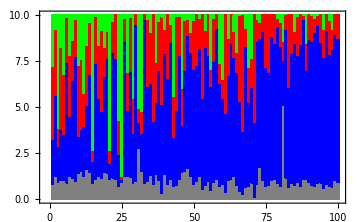

```mathematica
fixBarChart[fileV,2,250]
```

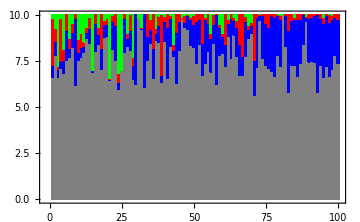

```mathematica
fixBarChart[fileV,4,250]
```

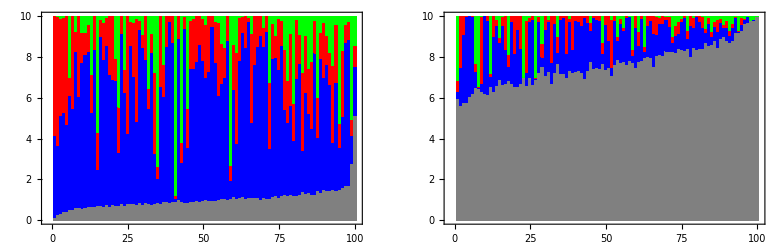

/Users/ailenemacpherson/Desktop/EcoEpiDrift/Plots/Eco_DirSel.pdf

```mathematica
GraphicsRow[{fixBarChart[fileV,2,250],fixBarChart[fileV,4,250]}]
Export[NotebookDirectory[]<>"Plots/Eco_DirSel.pdf",%,ImageResolution-> 300]
```